## Lagrangian

```mathematica
Quit[]
```

```mathematica
ClearAll["Global`*"]
```

### ODEs

#### No contact

```mathematica
RodOde[R:{__?NumericQ}]:=Block[
{Sol,S,s,nx,ny,x,y,θ,m},
Sol=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S]*(x[S]-px[S]),
ny'[S]==k γ[S](y[S]-py[S]),
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]]),
x[0]==0,y[0]==R[[2]],θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x[S],y[S],θ[S],s[S],nx[S],ny[S],m[S]},{S,0,L/2}][[1]];
{x[S]-L/2,y[S],θ[S]}/.Sol/.S->L/2
];

EquilSol[R_]:=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S]),
ny'[S]==k γ[S](y[S]-py[S]),
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]]),
x[0]==0,y[0]==R[[2]],θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x,y,θ,s,m,nx,ny},{S,0,L/2}][[1]];
```

```mathematica
(* With repulsion *)
RodOdeRepulsion[R:{__?NumericQ}]:=Block[
{Sol,S,s,nx,ny,x,y,θ,m},
Sol=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S]*(x[S]-px[S]) + γ[S]*Q/(x[S] - L/2*1.01)^n*HeavisideTheta[L/2-x[S]],
ny'[S]==k γ[S](y[S]-py[S]),
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]]),
x[0]==0,y[0]==R[[2]],θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x[S],y[S],θ[S],s[S],nx[S],ny[S],m[S]},{S,0,L/2}][[1]];
{x[S]-L/2,y[S],θ[S]}/.Sol/.S->L/2
];

EquilSolRepulsion[R_]:=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S])+ γ[S]*Q/(x[S] - L/2*1.01)^n*HeavisideTheta[L/2-x[S]],
ny'[S]==k γ[S](y[S]-py[S]),
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]]),
x[0]==0,y[0]==R[[2]],θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x,y,θ,s,m,nx,ny},{S,0,L/2}][[1]];
```

#### 1 Contact point

```mathematica
RodOdeContactPt[R:{__?NumericQ}]:=Block[
{Sol,Cond},
Sol=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S])-R[[5]]DiracDelta[S-R[[4]]],
ny'[S]==k γ[S](y[S]-py[S]),
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]]),
x[0]==0,y[0]==R[[2]],θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x[S],y[S],θ[S],s[S],nx[S],ny[S],m[S]},{S,0,L/2}][[1]];

Cond = {x[S]-δ,θ[S]+π/2}/.Sol/.S->R[[4]];

AppendTo[Cond,{x[S]-L/2,y[S],θ[S]}/.Sol/.S->L/2];
Flatten[Cond]
];
EquilSolnContactPt[R_]:=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S])-R[[5]]DiracDelta[S-R[[4]]],
ny'[S]==k γ[S](y[S]-py[S]),
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]]),
x[0]==0,y[0]==R[[2]],θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x,y,θ,s,nx,ny,m},{S,0,L/2}][[1]];
```

```mathematica
(* With repulsion *)
RodOdeContactPtRepulsion[R:{__?NumericQ}]:=Block[
{Sol,Cond},
Sol=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S])-R[[5]]DiracDelta[S-R[[4]]]+γ[S]*Q/(x[S] - L/2*1.01)^n*HeavisideTheta[L/2-x[S]],
ny'[S]==k γ[S](y[S]-py[S]),
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]]),
x[0]==0,y[0]==R[[2]],θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x[S],y[S],θ[S],s[S],nx[S],ny[S],m[S]},{S,0,L/2}][[1]];

Cond = {x[S]-δ,θ[S]+π/2}/.Sol/.S->R[[4]];

AppendTo[Cond,{x[S]-L/2,y[S],θ[S]}/.Sol/.S->L/2];
Flatten[Cond]
];
EquilSolnContactPtRepulsion[R_]:=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S])-R[[5]]DiracDelta[S-R[[4]]]+γ[S]*Q/(x[S] - L/2*1.01)^n*HeavisideTheta[L/2-x[S]],
ny'[S]==k γ[S](y[S]-py[S]),
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]]),
x[0]==0,y[0]==R[[2]],θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x,y,θ,s,nx,ny,m},{S,0,L/2}][[1]];
```

#### 1 Contact point, with area constraint

```mathematica
RodOdeContactPtAreaCons[R:{__?NumericQ}]:=Block[
{Sol,Cond},
(* R = {nx[0], y[0], m[0], sc, f - contact force, p - lagrange multiplier for area constraint *)
Sol=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S])-R[[5]]DiracDelta[S-R[[4]]]+R[[6]] Sin[θ[S]]UnitStep[R[[4]]-S],
ny'[S]==k γ[S](y[S]-py[S])-R[[6]]Cos[θ[S]]UnitStep[R[[4]]-S],
A'[S]==-x[S]γ[S]Sin[θ[S]],
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]]),
x[0]==0,y[0]==R[[2]],A[0]==0,θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x[S],y[S],A[S],θ[S],s[S],nx[S],ny[S],m[S]},{S,0,L/2}][[1]];

Cond = {x[S]-δ,θ[S]+π/2,A[S]-A0}/.Sol/.S->R[[4]];

AppendTo[Cond,{x[S]-L/2,y[S],θ[S]}/.Sol/.S->L/2];
Flatten[Cond]
];


EquilSolnContactPtAreaCons[R_]:=
NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S])-R[[5]]DiracDelta[S-R[[4]]]+R[[6]] Sin[θ[S]]UnitStep[R[[4]]-S],
ny'[S]==k γ[S](y[S]-py[S])-R[[6]]Cos[θ[S]]UnitStep[R[[4]]-S],
A'[S]==-x[S]γ[S]Sin[θ[S]],
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]]),
x[0]==0,y[0]==R[[2]],A[0]==0,θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x,y,θ,s,A,nx,ny,m},{S,0,L/2}][[1]];
RodOdeContactPtAreaConsRepulsion[R:{__?NumericQ}]:=Block[
{Sol,Cond},
(* R = {nx[0], y[0], m[0], sc, f - contact force, p - lagrange multiplier for area constraint *)
Sol=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S])-R[[5]]DiracDelta[S-R[[4]]]+R[[6]] Sin[θ[S]]UnitStep[R[[4]]-S]+γ[S]*Q/(x[S] - L/2*1.01)^n*UnitStep[L/2-x[S]],
ny'[S]==k γ[S](y[S]-py[S])-R[[6]]Cos[θ[S]]UnitStep[R[[4]]-S],
A'[S]==-x[S]γ[S]Sin[θ[S]],
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]]),
x[0]==0,y[0]==R[[2]],A[0]==0,θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x[S],y[S],A[S],θ[S],s[S],nx[S],ny[S],m[S]},{S,0,L/2}][[1]];

Cond = {x[S]-δ,θ[S]+π/2,A[S]-A0}/.Sol/.S->R[[4]];

AppendTo[Cond,{x[S]-L/2,y[S],θ[S]}/.Sol/.S->L/2];
Flatten[Cond]
];


EquilSolnContactPtAreaConsRepulsion[R_]:=
NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S])-R[[5]]DiracDelta[S-R[[4]]]+R[[6]] Sin[θ[S]]UnitStep[R[[4]]-S]+γ[S]*Q/(x[S] - L/2*1.01)^n*UnitStep[L/2-x[S]],
ny'[S]==k γ[S](y[S]-py[S])-R[[6]]Cos[θ[S]]UnitStep[R[[4]]-S],
A'[S]==-x[S]γ[S]Sin[θ[S]],
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]]),
x[0]==0,y[0]==R[[2]],A[0]==0,θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x,y,θ,s,A,nx,ny,m},{S,0,L/2}][[1]];
```

#### Contact region

```mathematica
RodOdeContactRegionAreaCons[R:{__?NumericQ}]:=Block[
{Sol,Cond,S1,S2,f,p,S},
(* R = {nx[0], y[0], m[0], S1, S2, f, p } *)

S1=R[[4]];
S2=R[[5]];
f=R[[6]];
p=R[[7]];

(* fixed area region; pre-contact *)
Sol=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S])+p Sin[θ[S]]UnitStep[S1-S]-f UnitStep[S-S1]UnitStep[S2-S],
ny'[S]==k γ[S](y[S]-py[S])-p Cos[θ[S]]UnitStep[S1-S],
A'[S]==-x[S]γ[S]Sin[θ[S]],
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]])(UnitStep[S1-S]+UnitStep[S-S2]),
x[0]==0,y[0]==R[[2]],A[0]==0,θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x[S],y[S],θ[S],A[S],s[S],nx[S],ny[S],m[S]},{S,0,L/2}][[1]];

Cond = {x[S]-δ,θ[S]+π/2,m[S],A[S]-A0}/.Sol/.S->S1;
AppendTo[Cond,{x[S]-L/2,y[S],θ[S]}/.Sol/.S->L/2];
Flatten[Cond]
];


EquilSolContactRegionAreaCons[R_]:=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S])+R[[7]] Sin[θ[S]]UnitStep[R[[4]]-S]-R[[6]] UnitStep[S-R[[4]]]UnitStep[R[[5]]-S],
ny'[S]==k γ[S](y[S]-py[S])-R[[7]] Cos[θ[S]]UnitStep[R[[4]]-S],
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]])(UnitStep[R[[4]]-S]+UnitStep[S-R[[5]]]),
x[0]==0,y[0]==R[[2]],θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x,y,s,θ,m,nx,ny},{S,0,L/2}][[1]];
```

```mathematica
(* Repulsion *)
RodOdeContactRegionRepulsion[R:{__?NumericQ}]:=Block[
{Sol,Cond,S1,S2,f,S},
(* R = {nx[0], y[0], m[0], S1, S2, f, p } *)

S1=R[[4]];
S2=R[[5]];
f=R[[6]];

(* fixed area region; pre-contact *)
Sol=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S])+γ[S]*Q/(x[S] - L/2*1.01)^n*HeavisideTheta[L/2-x[S]]-f UnitStep[S-S1]UnitStep[S2-S],
ny'[S]==k γ[S](y[S]-py[S]),
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]])(UnitStep[S1-S]+UnitStep[S-S2]),
x[0]==0,y[0]==R[[2]],θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x[S],y[S],θ[S],s[S],nx[S],ny[S],m[S]},{S,0,L/2}][[1]];

Cond = {x[S]-δ,θ[S]+π/2,m[S]}/.Sol/.S->S1;
AppendTo[Cond,{x[S]-L/2,y[S],θ[S]}/.Sol/.S->L/2];
Flatten[Cond]
];


EquilSolContactRegionRepulsion[R_]:=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S])+γ[S]*Q/(x[S] - L/2*1.01)^n*UnitStep[L/2-x[S]]-R[[6]] UnitStep[S-R[[4]]]UnitStep[R[[5]]-S],
ny'[S]==k γ[S](y[S]-py[S]),
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]])(UnitStep[R[[4]]-S]+UnitStep[S-R[[5]]]),
x[0]==0,y[0]==R[[2]],θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x,y,s,θ,m,nx,ny},{S,0,L/2}][[1]];
```

```mathematica
RodOdeContactRegionAreaConsRepulsion[R:{__?NumericQ}]:=Block[
{Sol,Cond,S1,S2,f,p,S},
(* R = {nx[0], y[0], m[0], S1, S2, f, p } *)

S1=R[[4]];
S2=R[[5]];
f=R[[6]];
p=R[[7]];

(* fixed area region; pre-contact *)
Sol=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S])+p Sin[θ[S]]UnitStep[S1-S]-f UnitStep[S-S1]UnitStep[S2-S]+γ[S]*Q/(x[S] - L/2*1.01)^n*UnitStep[L/2-x[S]],
ny'[S]==k γ[S](y[S]-py[S])-p Cos[θ[S]]UnitStep[S1-S],
A'[S]==-x[S]γ[S]Sin[θ[S]],
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]])(UnitStep[S1-S]+UnitStep[S-S2]),
x[0]==0,y[0]==R[[2]],A[0]==0,θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x[S],y[S],θ[S],A[S],s[S],nx[S],ny[S],m[S]},{S,0,L/2}][[1]];

Cond = {x[S]-δ,θ[S]+π/2,m[S],A[S]-A0}/.Sol/.S->S1;
AppendTo[Cond,{x[S]-L/2,y[S],θ[S]}/.Sol/.S->L/2];
Flatten[Cond]
];


EquilSolContactRegionAreaConsRepulsion[R_]:=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S])+R[[7]] Sin[θ[S]]UnitStep[R[[4]]-S]-R[[6]] UnitStep[S-R[[4]]]UnitStep[R[[5]]-S]+γ[S]*Q/(x[S] - L/2*1.01)^n*UnitStep[L/2-x[S]],
ny'[S]==k γ[S](y[S]-py[S])-R[[7]] Cos[θ[S]]UnitStep[R[[4]]-S],
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]])(UnitStep[R[[4]]-S]+UnitStep[S-R[[5]]]),
x[0]==0,y[0]==R[[2]],θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x,y,s,θ,m,nx,ny},{S,0,L/2}][[1]];
```

### Heterogeneous stiffness, uniform growth

#### Initial solution, parameters

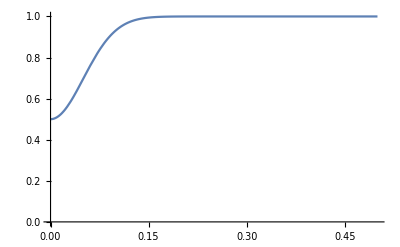

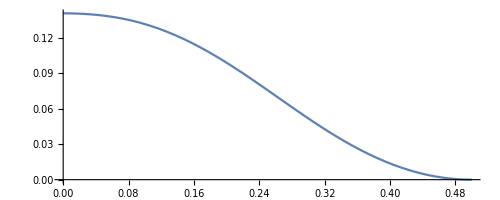

```mathematica
Clear[γ,R,Sol,sol,EB,px,py];
(* parameters *)
k=50;
dt=0.05;
dth = dt; (* initialising successful step size *)
δ=0.02;
L=1;
η=1;
γ[S_]=1+dt;
px[S_]:=S;
py[S_]:=0;
EB[s_]:=1-.5Exp[-s^2/(.005)];
Sol=FindRoot[RodOde[R],{R,{-42,0.1,-4}}];
Plot[EB[s],{s,0,1/2},PlotRange->{0,1}]
ParametricPlot[Evaluate[{x[S],y[S]}/.EquilSol[R/.Sol]],{S,0,L/2}]
```

#### Growth to contact

```mathematica
grs={};
(* first step *)
g=1+dt;
γ[S_]=g;
Sol=FindRoot[RodOde[R],{R,R/.Sol}];
sol=EquilSol[R/.Sol];
rs=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];

(* second step *)
g=g+dt;
γ[s_]=g;
Sol=FindRoot[RodOde[R],{R,R/.Sol}];
sol=EquilSol[R/.Sol];
re=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];

(* tracing *)
flag=0;
FailCount=0;
TOL=10^-6;
MaxDt=0.35;
MaxFails=60;

P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];
P2=Plot[(x[S]-δ)/.sol,{S,0,L/2}];

J1 = CreateWindow[DocumentNotebook[P1],WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
J2 = CreateWindow[DocumentNotebook[P2],WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];

(*Dynamic[Refresh[Show[P,PlotRange->All],UpdateInterval->$TimeUnit,TrackedSymbols->{P}],SynchronousUpdating->True]*)
rd
While[flag==0,
t = (re - rs);
g=g+dt;
γ[s_]=g;
Sol=Quiet[Reap[FindRoot[RodOde[R],{R,re+dt/dth*t}, StepMonitor :> Sow[R]]]];
Err=Norm[RodOde[R/.Sol[[1]]]];
If[Err > TOL, 
(* reject solution, decrease step size *)
FailCount = FailCount + 1; 
g=g-dt;
γ[s_]=g;
dt = 0.5 dt; Print[dt];If[FailCount == MaxFails, flag = 1,];,

(* else accept solution, store data, update foundation *)
sol=EquilSol[R/.Sol[[1]]];
rs = re;
re = R/.Sol[[1]];
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];

Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* update successful step size *)
dth=dt;

(* live plotting *)
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];
P2=Plot[(x[S]-δ)/.sol,{S,0,L/2}];
CreateWindow[DocumentNotebook[P1],J1,WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
 CreateWindow[DocumentNotebook[P2],J2,WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];
(*FinishDynamic[]*);

(* criteria to increase step size, based on number of steps to convergence of FindRoot *)steps = Length[Sol[[2]][[1]]];
If[steps < 4, dt = Min[1.25*dt, MaxDt]; Print[dt],];
];

];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

rd

0.0625

0.078125

0.0976563

0.12207

0.152588

$Aborted

```mathematica
NotebookClose[J1];NotebookClose[J2];
```

```mathematica
Manipulate[ParametricPlot[{x[s],y[s]}/.grs[[i,6]],{s,0,grs[[i,2]]/2},PlotRange->All],{i,1,Length[grs],1}]
```

Part::partw: Part 28 of {1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{« 1 »}}, {{0.0717392316014303`, 0.`}, {0.06818104513114749`, -0.09954080197360923`}, {0.060159623632330954`, -0.1670740276765533`}, {0.04974955455343316`, -0.20747197455805674`}, {0.037784031944335064`, -0.22336814170040242`}, {0.025035041908805112`, -« 19 »}, {0.01590328790973675`, -0.185918250708932`}, {0.00763978115905077`, -0.13831266412645762`}, {0.0008895562247268466`, -0.04941856185048861`}, {2.5009364002696112`*^-17, -8.593556630458366`*^-11}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ParametricPlot::plln: Limiting value 1/2\ « 1 » in {s, 0, 1/2\ grs ⟦ FE`i$$25, 2 ⟧} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 28, 2 ⟧ is longer than depth of object.

ParametricPlot::plln: Limiting value 1/2\ grs ⟦ 28, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$73, 2 ⟧} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 28, 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value 1/2\ grs ⟦ 28, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$73, 2 ⟧} is not a machine-sized real number.

Part::partw: Part 28 of {{1 + 0.05\ ⅇ^-39.0625\ S^2, 1, 1, « 3 », px, py}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ParametricPlot::plln: Limiting value 1 in {s, 0, 1/2\ grs ⟦ FE`i$$73, 2 ⟧} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 28, 2 ⟧ is longer than depth of object.

ParametricPlot::plln: Limiting value 1/2\ grs ⟦ 28, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$73, 2 ⟧} is not a machine-sized real number.

```mathematica
Manipulate[Plot[(x[s]-δ)/.grs[[i,6]],{s,0,L/2}],{i,1,Length[grs],1}]
```

Part::partd: Part specification grs ⟦ 1, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 1, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 1, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 1, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 1, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ReplaceAll::reps: {grs ⟦ 1, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

```mathematica
Save[ToString[$HomeDirectory]<>"/Dropbox/Research (unshared,current)/Morphorods/SelfContact/Lagrangian", grs]
```

```mathematica
re
```

{-3.8949,1.43702,-2.99537}

```mathematica
rs
```

{-3.97944,1.42976,-3.03567}

```mathematica
dt
```

8.43376×10^-7

```mathematica
dth
```

6.74701×10^-7

```mathematica
RodOde
```

#### First contact point

```mathematica
ii=27;
sc=0.33; (* guess for contact location *)
grs=Table[grs[[k]],{k,1,ii}];
γ[S_]=grs[[ii,1]];
R0=grs[[ii,5]];
R0=Flatten[AppendTo[R0,{sc,0, 0}]];
px=grs[[ii,7]];
py=grs[[ii,8]];
Sol=FindRoot[RodOdeContactPtAreaCons[R],{R,R0}];
sol=EquilSolnContactPtAreaCons[R/.Sol];
ParametricPlot[{x[S],y[S]}/.sol,{S,0,L/2}]
```

NDSolve::underdet: There are more dependent variables, {A[S], kγ[S], m[S], nx[S], ny[S], s[S], x[S], y[S], θ[S]}, than equations, so the system is underdetermined.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[« 1 » == 0y[0] == 1.2380911355028124`A[0] == 0θ[0] == 0s[0] == 0nx[0] == -6.436535170019177`ny[0] == 0m[0] == -3.737933592565668` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[x[0] == 0y[0] == 1.2380911355028124`A[0] == 0θ[0] == 0s[0] == 0nx[0] == -6.436535170019177`ny[0] == 0m[0] == -3.737933592565668` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[« 1 » == 0y[0] == 1.2380911355028124`A[0] == 0θ[0] == 0s[0] == 0nx[0] == -6.436535170019177`ny[0] == 0m[0] == -3.737933592565668` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::argt: ReplaceAll called with 3 arguments; 1 or 2 arguments are expected.

ReplaceAll::argt: ReplaceAll called with 4 arguments; 1 or 2 arguments are expected.

General::stop: Further output of ReplaceAll :: argt will be suppressed during this calculation.

FindRoot::nlnum: The function value ReplaceAll[{-0.02` + x[0.33`], 1.5707963267948966`  + θ[0.33`], -1.` A0 + A[0.33`]}, {« 1 »}, {« 1 »}, {SuperscriptBox[ is not a list of numbers with dimensions {1} at {R} = {{-6.43654, 1.23809, -3.73793, 0.33, 0., 0.}}.

NDSolve::underdet: There are more dependent variables, {A[S], kγ[S], m[S], nx[S], ny[S], s[S], x[S], y[S], θ[S]}, than equations, so the system is underdetermined.

FindRoot::nlnum: The function value ReplaceAll[{-0.02` + x[0.33`], 1.5707963267948966`  + θ[0.33`], -1.` A0 + A[0.33`]}, {« 1 »}, {« 1 »}, {SuperscriptBox[ is not a list of numbers with dimensions {1} at {R} = {{-6.43654, 1.23809, -3.73793, 0.33, 0., 0.}}.

NDSolve::underdet: There are more dependent variables, {A[S], kγ[S], m[S], nx[S], ny[S], s[S], x[S], y[S], θ[S]}, than equations, so the system is underdetermined.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[« 1 » == 0y[0] == 1.2380911355028124`A[0] == 0θ[0] == 0s[0] == 0nx[0] == -6.436535170019177`ny[0] == 0m[0] == -3.737933592565668` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[x[0] == 0y[0] == 1.2380911355028124`A[0] == 0θ[0] == 0s[0] == 0nx[0] == -6.436535170019177`ny[0] == 0m[0] == -3.737933592565668` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[« 1 » == 0y[0] == 1.2380911355028124`A[0] == 0θ[0] == 0s[0] == 0nx[0] == -6.436535170019177`ny[0] == 0m[0] == -3.737933592565668` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::argt: ReplaceAll called with 3 arguments; 1 or 2 arguments are expected.

ReplaceAll::argt: ReplaceAll called with 4 arguments; 1 or 2 arguments are expected.

General::stop: Further output of ReplaceAll :: argt will be suppressed during this calculation.

FindRoot::nlnum: The function value ReplaceAll[{-0.02` + x[0.33`], 1.5707963267948966`  + θ[0.33`], -1.` A0 + A[0.33`]}, {« 1 »}, {« 1 »}, {SuperscriptBox[ is not a list of numbers with dimensions {1} at {R} = {{-6.43654, 1.23809, -3.73793, 0.33, 0., 0.}}.

NDSolve::underdet: There are more dependent variables, {A[S], kγ[S], m[S], nx[S], ny[S], s[S], x[S], y[S], θ[S]}, than equations, so the system is underdetermined.

FindRoot::nlnum: The function value ReplaceAll[{-0.02` + x[0.33`], 1.5707963267948966`  + θ[0.33`], -1.` A0 + A[0.33`]}, {« 1 »}, {« 1 »}, {SuperscriptBox[ is not a list of numbers with dimensions {1} at {R} = {{-6.43654, 1.23809, -3.73793, 0.33, 0., 0.}}.

Part::partw: Part 5 of R/. FindRoot[RodOdeContactPtAreaCons[R], {R, R0}] does not exist.

NDSolve::underdet: There are more dependent variables, {A[S], kγ[S], m[S], nx[S], ny[S], s[S], x[S], y[S], θ[S]}, than equations, so the system is underdetermined.

General::stop: Further output of NDSolve :: underdet will be suppressed during this calculation.

FindRoot::nlnum: The function value ReplaceAll[{-0.02` + x[0.33`], 1.5707963267948966`  + θ[0.33`], -1.` A0 + A[0.33`]}, {« 1 »}, {« 1 »}, {SuperscriptBox[ is not a list of numbers with dimensions {1} at {R} = {{-6.43654, 1.23809, -3.73793, 0.33, 0., 0.}}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

Part::partw: Part 4 of R/. FindRoot[RodOdeContactPtAreaCons[R], {R, R0}] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

NDSolve::dsvar: 0. cannot be used as a variable.

NDSolve::ndinnt: Initial condition (R/. FindRoot[RodOdeContactPtAreaCons[R], {R, R0}]) ⟦ 3 ⟧ is not a number or a rectangular array of numbers.

NDSolve::dsvar: 0.0000102041 cannot be used as a variable.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[« 6 »θ[0] == 0s[0] == 0nx[0] == -6.436535170019177`ny[0] == 0m[0] == -3.737933592565668` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[« 1 » « 1 » « 1 »y[0] == 1.2380911355028124`A[0] == 0θ[0] == 0s[0] == 0nx[0] == -6.436535170019177`ny[0] == 0m[0] == -3.737933592565668` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[SuperscriptBox[« 6 »θ[0] == 0s[0] == 0nx[0] == -6.436535170019177`ny[0] == 0m[0] == -3.737933592565668` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::argt: ReplaceAll called with 3 arguments; 1 or 2 arguments are expected.

ReplaceAll::argt: ReplaceAll called with 4 arguments; 1 or 2 arguments are expected.

General::stop: Further output of ReplaceAll :: argt will be suppressed during this calculation.

FindRoot::nlnum: The function value {ReplaceAll[{-0.02 + x[0.33], 1.5708  + θ[0.33], -1.\ A0 + A[0.33]}, « 3 »]} is not a list of numbers with dimensions {1} at {R} = {{-6.43654, 1.23809, -3.73793, 0.33, 0., 0.}}.

Part::partw: Part 4 of R/. FindRoot[RodOdeContactPtAreaCons[R], {R, R0}] does not exist.

NDSolve::dsvar: 0.0000102041 cannot be used as a variable.

FindRoot::nlnum: The function value {ReplaceAll[{-0.02 + x[0.33], 1.5708  + θ[0.33], -1.\ A0 + A[0.33]}, « 3 »]} is not a list of numbers with dimensions {1} at {R} = {{-6.43654, 1.23809, -3.73793, 0.33, 0., 0.}}.

Part::partw: Part 4 of R/. FindRoot[RodOdeContactPtAreaCons[R], {R, R0}] does not exist.

NDSolve::dsvar: 0.0000102041 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

FindRoot::nlnum: The function value {ReplaceAll[{-0.02 + x[0.33], 1.5708  + θ[0.33], -1.\ A0 + A[0.33]}, « 3 »]} is not a list of numbers with dimensions {1} at {R} = {{-6.43654, 1.23809, -3.73793, 0.33, 0., 0.}}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

Part::partw: Part 4 of R/. FindRoot[RodOdeContactPtAreaCons[R], {R, R0}] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

NDSolve::underdet: There are more dependent variables, {A[S], kγ[S], m[S], nx[S], ny[S], s[S], x[S], y[S], θ[S]}, than equations, so the system is underdetermined.

General::stop: Further output of NDSolve :: underdet will be suppressed during this calculation.

-Graphics-

```mathematica
A0=-NIntegrate[x[S]y'[S]/.sol,{S,0,(R/.Sol)[[4]]}]
```

0.182148

```mathematica
rs=Flatten[AppendTo[R/.Sol,0]]
```

Set::write: Tag ReplaceAll in R/. {R → {-6.02071, 1.26449, -3.74703, 0.326621, -2.12607}} is Protected.

{-6.02071,1.26449,-3.74703,0.326621,-2.12607,0}

```mathematica
Sol=FindRoot[RodOdeContactPtAreaCons[R],{R,rs}];
sol=EquilSolnContactPtAreaCons[R/.Sol];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
g=γ[S]
```

3.71982

#### Evolving contact point; Seeking contact region

```mathematica
(* first step done above *)
(*g=3.825;*)
γ[S_]=g;
rs=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* second step *)
dt=0.005;
dth=dt; (* initialising successful dt *)
g=g+dt;
γ[S_]=g;
Sol=FindRoot[RodOdeContactPtAreaCons[R],{R,R/.Sol}];
sol=EquilSolnContactPtAreaCons[R/.Sol];
re=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,re,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* tracing *)
flag=0;
FailCount=0;
TOL=10^-4;
MaxDt=0.15;

P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];
P2=Plot[m[S]/.sol,{S,0,L/2}];

J1 = CreateWindow[DocumentNotebook[P1],WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
J2 = CreateWindow[DocumentNotebook[P2],WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];

(*Dynamic[Refresh[Show[P,PlotRange->All],UpdateInterval->$TimeUnit,TrackedSymbols->{P}],SynchronousUpdating->True]*)

While[flag==0,
t = (re - rs);
g=g+dt;
γ[S_]=g;

Sol=Quiet[Reap[FindRoot[RodOdeContactPtAreaCons[R],{R,re+dt/dth t}, StepMonitor :> Sow[R]]]];
Err=Norm[RodOdeContactPtAreaCons[R/.Sol[[1]]]];
If[Err > TOL, 
(* reject solution, decrease step size *)
FailCount = FailCount + 1; 
g=g-dt;
dt = 0.5 dt; Print[dt];If[FailCount == 100, flag = 1,];,

(* else accept solution, store data, update foundation *)
sol=EquilSolnContactPtAreaCons[ R/.Sol[[1]]];
rs = re;
re = R/.Sol[[1]];
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* update successful step size *)
dth=dt;

(* live plotting *)
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol],{S,0,L/2}];
P2=Plot[m[S]/.sol,{S,0,L/2}];
 CreateWindow[DocumentNotebook[P1],J1,WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
 CreateWindow[DocumentNotebook[P2],J2,WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];
(*FinishDynamic[]*)

(* criteria to increase step size, based on number of steps to convergence of FindRoot *)steps = Length[Sol[[2]][[1]]];
If[steps < 4, dt = Min[1.25*dt, MaxDt]; Print[dt],];
];

];
```

0.00625

0.0078125

0.00390625

0.00195313

0.00244141

0.00305176

0.0038147

0.00476837

0.00596046

0.00745058

0.00372529

0.00465661

0.00232831

0.00116415

0.00145519

0.00181899

0.00227374

0.00284217

0.00355271

0.00444089

0.00555112

0.00277556

0.00346945

0.00433681

0.00542101

0.00677626

0.00847033

0.0105879

0.0132349

0.0165436

0.00827181

0.0041359

0.00206795

0.00103398

0.000516988

0.000646235

0.000323117

0.000161559

0.0000807794

0.000100974

0.0000504871

0.0000252435

0.0000315544

0.0000157772

$Aborted

```mathematica
NotebookClose[J1];NotebookClose[J2];
```

```mathematica
ii=27;
```

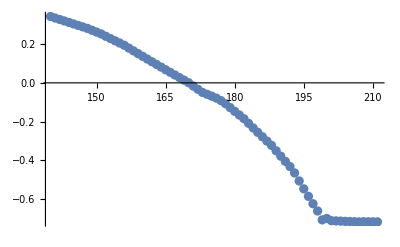

```mathematica
ListPlot[Table[{i,m[S]/.grs[[i,6]]/.S->grs[[i,5,4]]},{i,140,Length[grs]}]]
```

```mathematica
Save[ToString[$HomeDirectory]<>"/Dropbox/Research (unshared,current)/Morphorods/SelfContact/Lagrangian", grs]
```

```mathematica
grs=Get[ToString[$HomeDirectory]<>"/Dropbox/Research (unshared,current)/Morphorods/SelfContact/Lagrangian"];
```

```mathematica
rs
```

{-12.7635,1.62753,-3.8847,0.329691,29.5452,-89.9429}

```mathematica
re
```

{-12.7627,1.62759,-3.88447,0.32971,29.555,-89.9409}

```mathematica
Manipulate[ParametricPlot[{{-x[S],y[S]}/.grs[[i,6]],{x[S],y[S]}/.grs[[i,6]]},{S,0,L/2},PlotRange->All,PlotStyle->{Blue,Blue}],{i,1,Length[grs],1}]
Manipulate[Plot[m[S]/.grs[[i,6]],{S,0,L/2}],{i,1,Length[grs],1}]
```

Part::partw: Part 173 of {1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11579914359571852`, 0.21007930845062223`, 0.29986920038406517`, 0.3997266598642311`, 0.5`}}, {{0.00704715003623664`, 0.`}, {0.006354241591438223`, -0.013101676939791277`}, {0.004658135907468784`, -0.021651374946806204`}, {0.0026301532458439525`, -0.02223872562922858`}, {0.0007393483798990123`, -0.014223869549051419`}, {-2.025278648428969`*^-18, -3.179622472695829`*^-11}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}{1.1`, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {« 9 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 48 »« 103 » does not exist.

ReplaceAll::reps: {{1.05`, 1, 1 - 0.5` ⅇ^Times[« 2 »], 50, {« 1 »}, {« 1 »}, TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11579914359571852`, 0.21007930845062223`, 0.29986920038406517`, 0.3997266598642311`, 0.5`}}, {{0.00704715003623664`, 0.`}, {0.006354241591438223`, -0.013101676939791277`}, {0.004658135907468784`, -0.021651374946806204`}, {0.0026301532458439525`, -0.02223872562922858`}, {0.0007393483798990123`, -0.014223869549051419`}, {-2.025278648428969`*^-18, -3.179622472695829`*^-11}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 49 », « 103 »} ⟦ 173, 6 ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11579914359571852`, 0.21007930845062223`, 0.29986920038406517`, 0.3997266598642311`, 0.5`}}, {{0.00704715003623664`, 0.`}, {0.006354241591438223`, -0.013101676939791277`}, {0.004658135907468784`, -0.021651374946806204`}, {0.0026301532458439525`, -0.02223872562922858`}, {0.0007393483798990123`, -0.014223869549051419`}, {-2.025278648428969`*^-18, -3.179622472695829`*^-11}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}{1.1`, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {« 9 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 48 »« 103 » does not exist.

ReplaceAll::reps: {{1.05`, 1, 1 - 0.5` ⅇ^Times[« 2 »], 50, {« 1 »}, {« 1 »}, TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11579914359571852`, 0.21007930845062223`, 0.29986920038406517`, 0.3997266598642311`, 0.5`}}, {{0.00704715003623664`, 0.`}, {0.006354241591438223`, -0.013101676939791277`}, {0.004658135907468784`, -0.021651374946806204`}, {0.0026301532458439525`, -0.02223872562922858`}, {0.0007393483798990123`, -0.014223869549051419`}, {-2.025278648428969`*^-18, -3.179622472695829`*^-11}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 49 », « 103 »} ⟦ 173, 6 ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11579914359571852`, 0.21007930845062223`, 0.29986920038406517`, 0.3997266598642311`, 0.5`}}, {{0.00704715003623664`, 0.`}, {0.006354241591438223`, -0.013101676939791277`}, {0.004658135907468784`, -0.021651374946806204`}, {0.0026301532458439525`, -0.02223872562922858`}, {0.0007393483798990123`, -0.014223869549051419`}, {-2.025278648428969`*^-18, -3.179622472695829`*^-11}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}{1.1`, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {« 9 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 48 »« 103 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1, 1 - 0.5` ⅇ^Times[« 2 »], 50, {« 1 »}, {« 1 »}, TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11579914359571852`, 0.21007930845062223`, 0.29986920038406517`, 0.3997266598642311`, 0.5`}}, {{0.00704715003623664`, 0.`}, {0.006354241591438223`, -0.013101676939791277`}, {0.004658135907468784`, -0.021651374946806204`}, {0.0026301532458439525`, -0.02223872562922858`}, {0.0007393483798990123`, -0.014223869549051419`}, {-2.025278648428969`*^-18, -3.179622472695829`*^-11}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 49 », « 103 »} ⟦ 173, 6 ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ParametricPlot::plln: Limiting value L/2 in {S, 0, L/2} is not a machine-sized real number.

Plot::plln: Limiting value L/2 in {S, 0, L/2} is not a machine-sized real number.

ParametricPlot::plln: Limiting value L/2 in {S, 0, L/2} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Global`L/2 in {Global`S, 0, Global`L/2} is not a machine-sized real number.

Plot::plln: Limiting value Global`L/2 in {Global`S, 0, Global`L/2} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Global`L/2 in {Global`S, 0, Global`L/2} is not a machine-sized real number.

Plot::plln: Limiting value Global`L/2 in {Global`S, 0, Global`L/2} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Global`L/2 in {Global`S, 0, Global`L/2} is not a machine-sized real number.

Plot::plln: Limiting value Global`L/2 in {Global`S, 0, Global`L/2} is not a machine-sized real number.

ParametricPlot::plln: Limiting value L/2 in {S, 0, L/2} is not a machine-sized real number.

Plot::plln: Limiting value L/2 in {S, 0, L/2} is not a machine-sized real number.

ParametricPlot::plln: Limiting value L/2 in {S, 0, L/2} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 173, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 173, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 173, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 173, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 173, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 153, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 153, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 153, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 153, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 153, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ReplaceAll::reps: {grs ⟦ 153, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 153, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 153, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 153, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 153, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 153, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ReplaceAll::reps: {grs ⟦ 153, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 173, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 173, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 173, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 173, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 173, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partw: Part 173 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {10.202149658203126`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {10.202149658203126`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 24 »{10.202149658203126`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 153 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {10.202149658203126`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 153 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 24 »{10.202149658203126`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 153 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {10.202149658203126`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 173 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 27 », {3.3726562500000004`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 27 », {3.3726562500000004`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 27 », {3.3726562500000004`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 153 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 27 », {3.3726562500000004`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 153 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 27 »{3.3726562500000004`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 153 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 27 », {3.3726562500000004`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 173 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 35 »{3.670991077423096`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, « 6 », TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 153 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 153 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 35 »{3.670991077423096`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

ReplaceAll::reps: {{1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, « 6 », TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 153 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 173 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 35 »{3.670991077423096`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, « 6 », TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 153 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 153 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 35 »{3.670991077423096`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

ReplaceAll::reps: {{1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, « 6 », TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 153 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 173 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {4.770912109375001`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {4.770912109375001`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {4.770912109375001`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 153 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {4.770912109375001`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 153 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 24 »{4.770912109375001`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

ReplaceAll::reps: {{1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {4.770912109375001`, « 6 », TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 153 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {4.770912109375001`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 153 of {1.1`, 1, 1, « 3 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {15}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, « 13 », 0.5`}}, {{0.18169222147950959`, 0.`}, {0.17474847845124378`, -0.2943128871883476`}, {0.16235918459213264`, -0.4649537470277443`}, {0.14301306135332115`, -0.6021616147941079`}, {0.12173053039804468`, -0.6764058712346361`}, « 6 », {-0.0009156838126685559`, -0.044478470971068315`}, {-0.0012253259742081271`, 0.017839720586314577`}, {-0.0003208751814295223`, 0.025140385964973446`}, {4.417090764160549`*^-15, 2.979045669899779`*^-10}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 28 » does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 153, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 153 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.1`, 1.`, 1.`, 868.0555555555555`, {-93.58602209811309`, « 20 », -5.47563602000443`}, {x → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], y → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], θ → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], 0.000010214285714285712` → 0.000010214285714285712`, m → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], nx → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], ny → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 28 »} ⟦ 153, 6 ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 153 of {1.1`, 1, 1, « 3 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {15}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, « 13 », 0.5`}}, {{0.18169222147950959`, 0.`}, {0.17474847845124378`, -0.2943128871883476`}, {0.16235918459213264`, -0.4649537470277443`}, {0.14301306135332115`, -0.6021616147941079`}, {0.12173053039804468`, -0.6764058712346361`}, « 6 », {-0.0009156838126685559`, -0.044478470971068315`}, {-0.0012253259742081271`, 0.017839720586314577`}, {-0.0003208751814295223`, 0.025140385964973446`}, {4.417090764160549`*^-15, 2.979045669899779`*^-10}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 28 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{« 1 »} ⟦ 153, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 173 of {1.1`, 1, 1, « 3 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {15}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, « 13 », 0.5`}}, {{0.18169222147950959`, 0.`}, {0.17474847845124378`, -0.2943128871883476`}, {0.16235918459213264`, -0.4649537470277443`}, {0.14301306135332115`, -0.6021616147941079`}, {0.12173053039804468`, -0.6764058712346361`}, « 6 », {-0.0009156838126685559`, -0.044478470971068315`}, {-0.0012253259742081271`, 0.017839720586314577`}, {-0.0003208751814295223`, 0.025140385964973446`}, {4.417090764160549`*^-15, 2.979045669899779`*^-10}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 28 » does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 173, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {1.1`, 1, 1, « 3 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {15}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, « 13 », 0.5`}}, {{0.18169222147950959`, 0.`}, {0.17474847845124378`, -0.2943128871883476`}, {0.16235918459213264`, -0.4649537470277443`}, {0.14301306135332115`, -0.6021616147941079`}, {0.12173053039804468`, -0.6764058712346361`}, « 6 », {-0.0009156838126685559`, -0.044478470971068315`}, {-0.0012253259742081271`, 0.017839720586314577`}, {-0.0003208751814295223`, 0.025140385964973446`}, {4.417090764160549`*^-15, 2.979045669899779`*^-10}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 28 » does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 173, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 153 of {{(1 + 0.05\ ⅇ^-6.25\ Power[« 2 »])^2[0.0000102143], 1, 1, 868.056, rs, sol, px, py}} does not exist.

ReplaceAll::reps: {{{(1 + 0.05\ Power[« 2 »])^2[0.0000102143], 1, 1, 868.056, rs, sol, px, py}} ⟦ 153, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 153 of {{(1 + 0.05\ ⅇ^-6.25\ Power[« 2 »])^2[0.0000102143], 1, 1, 868.056, rs, sol, px, py}} does not exist.

ReplaceAll::reps: {{{(1 + 0.05\ Power[« 2 »])^2[0.0000102143], 1, 1, 868.056, rs, sol, px, py}} ⟦ 153, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 153 of {{(1.  + 0.05\ 2.71828^-6.25\ Power[« 2 »])^2[0.0000102143], 1., 1., 868.056, rs, sol, px, py}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{{(1.  + 0.05\ Power[« 2 »])^2[0.0000102143], 1., 1., 868.056, rs, sol, px, py}} ⟦ 153, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 173 of {1.0499999997966343`, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {« 1 »}, {{0.03436278249570261`, 0.`}, {0.03196757607716958`, -0.07589878150860022`}, {0.026902738417898357`, -0.1185170072048991`}, {0.020068476474868584`, -0.13486663229980686`}, {0.012756060608479258`, -0.12414822120927134`}, « 1 », {0.0009484620927244481`, -0.030547182608392037`}, {-0.000027791672536957957`, -0.0032992829045550578`}, {-3.6090495494371057`*^-7, 0.00030019591840245484`}, {-4.4911039848960234`*^-15, 3.9013766223762537`*^-13}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {1.0499999997966343`, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {« 1 »}, {{0.03436278249570261`, 0.`}, {0.03196757607716958`, -0.07589878150860022`}, {0.026902738417898357`, -0.1185170072048991`}, {0.020068476474868584`, -0.13486663229980686`}, {0.012756060608479258`, -0.12414822120927134`}, « 1 », {0.0009484620927244481`, -0.030547182608392037`}, {-0.000027791672536957957`, -0.0032992829045550578`}, {-3.6090495494371057`*^-7, 0.00030019591840245484`}, {-4.4911039848960234`*^-15, 3.9013766223762537`*^-13}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {1.0499999997966343`, 1.`, « 4 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 0, {11}, {4}, 0, 0, 0, 0, Automatic, {}, {}, False}, « 1 », {Developer`PackedArrayForm, {0, 1, 2, « 7 », 10, 11}, {0.`, 0.051143004552117954`, 0.10174658192472008`, « 6 », 0.4499998594818033`, 0.49999999999999684`}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.06089182482681007`, 0.11189504279106804`, 0.16484777875120654`, 0.22041302829215925`, 0.28232020467271113`, 0.368960502530721`, 0.43372506630267005`, 0.4976369442889068`, 0.5`}}, « 1 », {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 153 of {1.0499999997962273`, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {« 1 »}, {{0.03436278249570261`, 0.`}, {0.03196757607716958`, -0.07589878150860022`}, {0.026902738417898357`, -0.1185170072048991`}, {0.020068476474868584`, -0.13486663229980686`}, {0.012756060608479258`, -0.12414822120927134`}, « 1 », {0.0009484620927244481`, -0.030547182608392037`}, {-0.000027791672536957957`, -0.0032992829045550578`}, {-3.6090495494371057`*^-7, 0.00030019591840245484`}, {-4.4911039848960234`*^-15, 3.9013766223762537`*^-13}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 153 of {1.0499999997962273`, 1.`, « 4 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 0, {11}, {4}, 0, 0, 0, 0, Automatic, {}, {}, False}, « 1 », {Developer`PackedArrayForm, {0, 1, 2, « 7 », 10, 11}, {0.`, 0.051143004552117954`, 0.10174658192472008`, « 6 », 0.4499998594818033`, 0.49999999999999684`}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.06089182482681007`, 0.11189504279106804`, 0.16484777875120654`, 0.22041302829215925`, 0.28232020467271113`, 0.368960502530721`, 0.43372506630267005`, 0.4976369442889068`, 0.5`}}, « 1 », {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 153 of {1.0497966415441924`, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {« 1 »}, {{0.03436278249570261`, 0.`}, {0.03196757607716958`, -0.07589878150860022`}, {0.026902738417898357`, -0.1185170072048991`}, {0.020068476474868584`, -0.13486663229980686`}, {0.012756060608479258`, -0.12414822120927134`}, « 1 », {0.0009484620927244481`, -0.030547182608392037`}, {-0.000027791672536957957`, -0.0032992829045550578`}, {-3.6090495494371057`*^-7, 0.00030019591840245484`}, {-4.4911039848960234`*^-15, 3.9013766223762537`*^-13}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 173 of {{1.05, 1, 1, « 3 », px, py}} does not exist.

ReplaceAll::reps: {{1.0499999997966343`, 1, 1, 868.0555555555554`, {-113.00007924868558`, 0.06872556499140522`, -2.4293636642406775`}, {x → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], y → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], θ → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], s → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], m → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], nx → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], ny → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, px, py}} ⟦ 173, 6 ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {{1.05, 1, 1, « 3 », px, py}} does not exist.

ReplaceAll::reps: {{1.0499999997966343`, 1, 1, 868.0555555555554`, {-113.00007924868558`, 0.06872556499140522`, -2.4293636642406775`}, {x → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], y → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], θ → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], s → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], m → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], nx → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], ny → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, px, py}} ⟦ 173, 6 ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {{1.05, 1., 1., 868.056, {-113., 0.0687256, -2.42936}, {« 1 »}, px, py}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.0499999997966343`, 1.`, 1.`, 868.0555555555554`, {-113.00007924868558`, 0.06872556499140522`, -2.4293636642406775`}, {x → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], y → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], θ → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], s → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], m → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], nx → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], ny → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, px, py}} ⟦ 173, 6 ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 153, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 153, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 153, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 153, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 153, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ReplaceAll::reps: {grs ⟦ 153, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 173, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 173, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 173, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 173, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 173, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partw: Part 173 of {« 1 »} does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 173, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {« 1 »} does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 173, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 0, {11}, {4}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.05`, 0.1`, 0.15`, 0.2`, 0.25`, 0.3`, 0.35`, 0.4`, 0.45`, 0.5`}}, {Developer`PackedArrayForm, {0, 1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11}, {1.0201`, 1.0182040932854977`, 1.01353138387918`, 1.0082656701454762`, 1.0041539698336965`, 1.0017183037897288`, 1.0005850064773865`, 1.0001638863465911`, 1.0000377715880888`, 1.0000071612315142`, 1.000001116851729`}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]], 1.`, « 4 », TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 49 »« 48 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 0, {11}, {4}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.05`, 0.1`, 0.15`, 0.2`, 0.25`, 0.3`, 0.35`, 0.4`, 0.45`, 0.5`}}, {Developer`PackedArrayForm, {0, 1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11}, {1.0201`, 1.0182040932854977`, 1.01353138387918`, 1.0082656701454762`, 1.0041539698336965`, 1.0017183037897288`, 1.0005850064773865`, 1.0001638863465911`, 1.0000377715880888`, 1.0000071612315142`, 1.000001116851729`}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]], 1.`, « 4 », TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 49 », « 48 »} ⟦ 173, 6 ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 153 of {« 1 »} does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 153, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 153 of {TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 0, {11}, {4}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.05`, 0.1`, 0.15`, 0.2`, 0.25`, 0.3`, 0.35`, 0.4`, 0.45`, 0.5`}}, {Developer`PackedArrayForm, {0, 1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11}, {1.0201`, 1.0182040932854977`, 1.01353138387918`, 1.0082656701454762`, 1.0041539698336965`, 1.0017183037897288`, 1.0005850064773865`, 1.0001638863465911`, 1.0000377715880888`, 1.0000071612315142`, 1.000001116851729`}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]], 1.`, « 4 », TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 49 »« 48 » does not exist.

ReplaceAll::reps: {{TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 0, {11}, {4}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.05`, 0.1`, 0.15`, 0.2`, 0.25`, 0.3`, 0.35`, 0.4`, 0.45`, 0.5`}}, {Developer`PackedArrayForm, {0, 1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11}, {1.0201`, 1.0182040932854977`, 1.01353138387918`, 1.0082656701454762`, 1.0041539698336965`, 1.0017183037897288`, 1.0005850064773865`, 1.0001638863465911`, 1.0000377715880888`, 1.0000071612315142`, 1.000001116851729`}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]], 1.`, « 4 », TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 49 », « 48 »} ⟦ 153, 6 ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 153 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{« 1 »} ⟦ 153, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 173 of {TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]], 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {9}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, « 7 », 0.5`}}, {{0.03515088097123734`, 0.`}, {0.034248293493059696`, -0.028500768104017804`}, {0.03072935350360036`, -0.0761860935148592`}, {0.023954647709545463`, -0.12190573304105744`}, {0.01721040413170269`, -0.13486716797179804`}, {0.009948268086007211`, -0.11917613444033752`}, {0.0033255560922190483`, -0.06960715346524878`}, {0.000372970250186428`, -0.018589267547764948`}, {-1.6908636632135457`*^-17, 2.676737430307502`*^-16}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 49 »« 59 » does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 173, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]], 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {9}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, « 7 », 0.5`}}, {{0.03515088097123734`, 0.`}, {0.034248293493059696`, -0.028500768104017804`}, {0.03072935350360036`, -0.0761860935148592`}, {0.023954647709545463`, -0.12190573304105744`}, {0.01721040413170269`, -0.13486716797179804`}, {0.009948268086007211`, -0.11917613444033752`}, {0.0033255560922190483`, -0.06960715346524878`}, {0.000372970250186428`, -0.018589267547764948`}, {-1.6908636632135457`*^-17, 2.676737430307502`*^-16}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 49 »« 59 » does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 173, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]], 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {9}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, « 7 », 0.5`}}, {{0.03515088097123734`, 0.`}, {0.034248293493059696`, -0.028500768104017804`}, {0.03072935350360036`, -0.0761860935148592`}, {0.023954647709545463`, -0.12190573304105744`}, {0.01721040413170269`, -0.13486716797179804`}, {0.009948268086007211`, -0.11917613444033752`}, {0.0033255560922190483`, -0.06960715346524878`}, {0.000372970250186428`, -0.018589267547764948`}, {-1.6908636632135457`*^-17, 2.676737430307502`*^-16}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 49 »« 59 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{« 1 »} ⟦ 173, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 153 of {TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]], 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {9}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, « 7 », 0.5`}}, {{0.03515088097123734`, 0.`}, {0.034248293493059696`, -0.028500768104017804`}, {0.03072935350360036`, -0.0761860935148592`}, {0.023954647709545463`, -0.12190573304105744`}, {0.01721040413170269`, -0.13486716797179804`}, {0.009948268086007211`, -0.11917613444033752`}, {0.0033255560922190483`, -0.06960715346524878`}, {0.000372970250186428`, -0.018589267547764948`}, {-1.6908636632135457`*^-17, 2.676737430307502`*^-16}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 49 »« 59 » does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 153, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 153 of {« 1 »}{TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]], 1.`, 1.`  - 0.8` 2.718281828459045`^-39.0625` s^2, « 18 », {« 1 »}, {« 1 »}, TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 0, {11}, {4}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.05`, 0.1`, 0.15`, 0.2`, 0.25`, 0.3`, 0.35`, 0.4`, 0.45`, 0.5`}}, {Developer`PackedArrayForm, {0, 1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11}, {0.`, 0.05120537967384769`, 0.10215154822647916`, 0.1526140045605995`, 0.20246426904807283`, 0.2518043949918912`, 0.300984436388711`, 0.35036649487357263`, 0.40007633394303155`, 0.45000481234239237`, 0.5`}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 48 »« 59 » does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 153, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 153 of {TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]], 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {9}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, « 7 », 0.5`}}, {{0.03515088097123734`, 0.`}, {0.034248293493059696`, -0.028500768104017804`}, {0.03072935350360036`, -0.0761860935148592`}, {0.023954647709545463`, -0.12190573304105744`}, {0.01721040413170269`, -0.13486716797179804`}, {0.009948268086007211`, -0.11917613444033752`}, {0.0033255560922190483`, -0.06960715346524878`}, {0.000372970250186428`, -0.018589267547764948`}, {-1.6908636632135457`*^-17, 2.676737430307502`*^-16}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 49 »« 59 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{« 1 »} ⟦ 153, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 173 of {TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]], 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {9}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, « 7 », 0.5`}}, {{0.03515088097123734`, 0.`}, {0.034248293493059696`, -0.028500768104017804`}, {0.03072935350360036`, -0.0761860935148592`}, {0.023954647709545463`, -0.12190573304105744`}, {0.01721040413170269`, -0.13486716797179804`}, {0.009948268086007211`, -0.11917613444033752`}, {0.0033255560922190483`, -0.06960715346524878`}, {0.000372970250186428`, -0.018589267547764948`}, {-1.6908636632135457`*^-17, 2.676737430307502`*^-16}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 49 »« 63 » does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 173, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]], 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {9}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, « 7 », 0.5`}}, {{0.03515088097123734`, 0.`}, {0.034248293493059696`, -0.028500768104017804`}, {0.03072935350360036`, -0.0761860935148592`}, {0.023954647709545463`, -0.12190573304105744`}, {0.01721040413170269`, -0.13486716797179804`}, {0.009948268086007211`, -0.11917613444033752`}, {0.0033255560922190483`, -0.06960715346524878`}, {0.000372970250186428`, -0.018589267547764948`}, {-1.6908636632135457`*^-17, 2.676737430307502`*^-16}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 49 »« 63 » does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 173, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 173 of {« 1 »}{TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]], 1.`, 1.`  - 0.8` 2.718281828459045`^-39.0625` s^2, « 18 », {« 1 »}, {« 1 »}, TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 0, {11}, {4}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.05`, 0.1`, 0.15`, 0.2`, 0.25`, 0.3`, 0.35`, 0.4`, 0.45`, 0.5`}}, {Developer`PackedArrayForm, {0, 1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11}, {0.`, 0.05120537967384769`, 0.10215154822647916`, 0.1526140045605995`, 0.20246426904807283`, 0.2518043949918912`, 0.300984436388711`, 0.35036649487357263`, 0.40007633394303155`, 0.45000481234239237`, 0.5`}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 48 »« 63 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{« 1 »} ⟦ 173, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

#### First contact region solution

```mathematica
Length[grs]
```

173

```mathematica
ii=153;
m[S]/.grs[[ii,6]]/.S->grs[[ii,5,4]]
grs=Table[grs[[k]],{k,1,ii}];
```

-0.110452

```mathematica
A0
```

0.182148

```mathematica
NumberForm[0.18214782625416231,16]
```

0.1821478262541623

```mathematica
(*A0=0.20618879019655859;*)
γ[S_]=grs[[ii,1]];
px=grs[[ii,7]];
py=grs[[ii,8]];
R0=grs[[ii,5]];
eps=0.01;
R0={R0[[1]],R0[[2]],R0[[3]],R0[[4]]-eps,R0[[4]]+eps,R0[[5]]/2/eps,R0[[6]]};
```

```mathematica
RodOdeContactPtAreaCons[R0]
```

{0.0611025,8.68424,-0.248748,-0.204346,1.07916,6.20372}

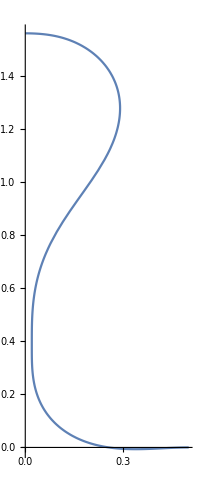

```mathematica
Sol=FindRoot[RodOdeContactRegion[R],{R,R0},AccuracyGoal->6,MaxIterations->Infinity,PrecisionGoal->6];
sol=EquilSolContactRegion[R/.Sol];
ParametricPlot[{x[S],y[S]}/.sol,{S,0,L/2}]
```

```mathematica
Norm[RodOdeContactRegion[R/.Sol]]
```

4.64913×10^-9

```mathematica
R/.Sol
```

{-13.027,1.56028,-3.95468,0.324096,0.328602,5833.8,-87.3043}

```mathematica
g=γ[S]
```

4.30051

#### Contact region

```mathematica
γ[S_]=g;
rs=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* second step *)
dt=0.001;
dth=dt; (* initialising successful dt *)
g=g+dt;
γ[S_]=g;
Sol=FindRoot[RodOdeContactRegion[R],{R,R/.Sol}];
sol=EquilSolContactRegion[R/.Sol];
re=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,re,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];

(* tracing *)
flag=0;
FailCount=0;
TOL=10^-4;
MaxDt=0.15;

P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];

J1 = CreateWindow[DocumentNotebook[P1],WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];

(*Dynamic[Refresh[Show[P,PlotRange->All],UpdateInterval->$TimeUnit,TrackedSymbols->{P}],SynchronousUpdating->True]*)

While[flag==0,
t = (re - rs);
g=g+dt;
γ[S_]=g;

Sol=Quiet[Reap[FindRoot[RodOdeContactRegion[R],{R,re+dt/dth t}, StepMonitor :> Sow[R]]]];
Err=Norm[RodOdeContactRegion[R/.Sol[[1]]]];
If[Err > TOL, 
(* reject solution, decrease step size *)
FailCount = FailCount + 1; 
g=g-dt;
dt = 0.5 dt; Print[dt];If[FailCount == 200, flag = 1,];,

(* else accept solution, store data, update foundation *)
sol=EquilSolContactRegion[R/.Sol[[1]]];
rs = re;
re = R/.Sol[[1]];
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* update successful step size *)
dth=dt;

(* live plotting *)
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol],{S,0,L/2}];
CreateWindow[DocumentNotebook[P1],J1,WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
 
(* criteria to increase step size, based on number of steps to convergence of FindRoot *)steps = Length[Sol[[2]][[1]]];
If[steps < 4, dt = Min[1.25*dt, MaxDt]; Print[dt],];
];

];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.00125

0.0015625

0.00195313

0.00244141

0.00305176

0.0038147

0.00476837

0.00596046

0.00745058

0.00931323

0.0116415

0.0145519

0.0181899

0.0227374

0.0284217

0.0355271

0.0177636

0.0222045

0.0277556

0.0346945

0.0433681

0.0542101

0.0677626

0.0847033

0.0423516

0.0211758

$Aborted

```mathematica
NotebookClose[J1]
```

```mathematica
Length[grs]
```

313

```mathematica
Save[ToString[$HomeDirectory]<>"/Dropbox/Research (unshared,current)/Morphorods/SelfContact/Lagrangian", grs]
```

```mathematica
grs=Get[ToString[$HomeDirectory]<>"/Dropbox/Research (unshared,current)/Morphorods/SelfContact/Lagrangian"];
```

```mathematica
Manipulate[ParametricPlot[{{-x[S],y[S]}/.grs[[i,6]],{x[S],y[S]}/.grs[[i,6]]},{S,0,1/2},PlotRange->{{-1,1},{-1,2.5}}],{i,1,Length[grs],1}]
```

Part::partd: Part specification grs ⟦ 275, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 275, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 275, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 275, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 275, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 275, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 275, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 275, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 275, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 275, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification Global`grs ⟦ 275, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {Global`grs ⟦ 275, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification Global`grs ⟦ 275, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {Global`grs ⟦ 275, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification Global`grs ⟦ 275, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification Global`grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {Global`grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification Global`grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {Global`grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification Global`grs ⟦ 160, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification Global`grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {Global`grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification Global`grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {Global`grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification Global`grs ⟦ 160, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ReplaceAll::reps: {grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partw: Part 275 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {10.202149658203126`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {10.202149658203126`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 24 »{10.202149658203126`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 160 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {10.202149658203126`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 160 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {10.202149658203126`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 160 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 24 »{10.202149658203126`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 275 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 27 », {3.3726562500000004`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 27 », {3.3726562500000004`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 27 »{3.3726562500000004`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 160 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 27 », {3.3726562500000004`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 160 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 27 », {3.3726562500000004`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 160 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 27 »{3.3726562500000004`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 160 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 160 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 160 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 35 »{3.670991077423096`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, « 6 », TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 275 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 35 »{3.670991077423096`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, « 6 », TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 160 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 160 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 160 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 35 »{3.670991077423096`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, « 6 », TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 275 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 35 »{3.670991077423096`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, « 6 », TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 275 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {4.770912109375001`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {4.770912109375001`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 24 »{4.770912109375001`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {4.770912109375001`, « 6 », TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 160 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {4.770912109375001`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 160 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {4.770912109375001`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 160 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 24 »{4.770912109375001`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {4.770912109375001`, « 6 », TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 275 of {1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 49 »« 183 » does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, {1.1`, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {« 9 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 48 », « 183 »} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 49 »« 183 » does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, {1.1`, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {« 9 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 48 », « 183 »} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 49 »« 183 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, {1.1`, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {« 9 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 48 », « 183 »} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 275 of {1.1`, 1, 1, « 3 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {15}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, « 13 », 0.5`}}, {{0.18169222147950959`, 0.`}, {0.17474847845124378`, -0.2943128871883476`}, {0.16235918459213264`, -0.4649537470277443`}, {0.14301306135332115`, -0.6021616147941079`}, {0.12173053039804468`, -0.6764058712346361`}, « 6 », {-0.0009156838126685559`, -0.044478470971068315`}, {-0.0012253259742081271`, 0.017839720586314577`}, {-0.0003208751814295223`, 0.025140385964973446`}, {4.417090764160549`*^-15, 2.979045669899779`*^-10}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 28 » does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 275, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {1.1`, 1, 1, « 3 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {15}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, « 13 », 0.5`}}, {{0.18169222147950959`, 0.`}, {0.17474847845124378`, -0.2943128871883476`}, {0.16235918459213264`, -0.4649537470277443`}, {0.14301306135332115`, -0.6021616147941079`}, {0.12173053039804468`, -0.6764058712346361`}, « 6 », {-0.0009156838126685559`, -0.044478470971068315`}, {-0.0012253259742081271`, 0.017839720586314577`}, {-0.0003208751814295223`, 0.025140385964973446`}, {4.417090764160549`*^-15, 2.979045669899779`*^-10}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 28 » does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 275, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 160 of {1.1`, 1, 1, « 3 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {15}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, « 13 », 0.5`}}, {{0.18169222147950959`, 0.`}, {0.17474847845124378`, -0.2943128871883476`}, {0.16235918459213264`, -0.4649537470277443`}, {0.14301306135332115`, -0.6021616147941079`}, {0.12173053039804468`, -0.6764058712346361`}, « 6 », {-0.0009156838126685559`, -0.044478470971068315`}, {-0.0012253259742081271`, 0.017839720586314577`}, {-0.0003208751814295223`, 0.025140385964973446`}, {4.417090764160549`*^-15, 2.979045669899779`*^-10}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 28 » does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 160 of {1.1`, 1, 1, « 3 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {15}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, « 13 », 0.5`}}, {{0.18169222147950959`, 0.`}, {0.17474847845124378`, -0.2943128871883476`}, {0.16235918459213264`, -0.4649537470277443`}, {0.14301306135332115`, -0.6021616147941079`}, {0.12173053039804468`, -0.6764058712346361`}, « 6 », {-0.0009156838126685559`, -0.044478470971068315`}, {-0.0012253259742081271`, 0.017839720586314577`}, {-0.0003208751814295223`, 0.025140385964973446`}, {4.417090764160549`*^-15, 2.979045669899779`*^-10}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 28 » does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 160 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 275 of {1.1`, 1, 1, « 3 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {15}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, « 13 », 0.5`}}, {{0.18169222147950959`, 0.`}, {0.17474847845124378`, -0.2943128871883476`}, {0.16235918459213264`, -0.4649537470277443`}, {0.14301306135332115`, -0.6021616147941079`}, {0.12173053039804468`, -0.6764058712346361`}, « 6 », {-0.0009156838126685559`, -0.044478470971068315`}, {-0.0012253259742081271`, 0.017839720586314577`}, {-0.0003208751814295223`, 0.025140385964973446`}, {4.417090764160549`*^-15, 2.979045669899779`*^-10}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 28 » does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 275, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {1.1`, 1, 1, « 3 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {15}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, « 13 », 0.5`}}, {{0.18169222147950959`, 0.`}, {0.17474847845124378`, -0.2943128871883476`}, {0.16235918459213264`, -0.4649537470277443`}, {0.14301306135332115`, -0.6021616147941079`}, {0.12173053039804468`, -0.6764058712346361`}, « 6 », {-0.0009156838126685559`, -0.044478470971068315`}, {-0.0012253259742081271`, 0.017839720586314577`}, {-0.0003208751814295223`, 0.025140385964973446`}, {4.417090764160549`*^-15, 2.979045669899779`*^-10}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 28 » does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 275, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 160 of {1.1`, 1, 1, « 3 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {15}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, « 13 », 0.5`}}, {{0.18169222147950959`, 0.`}, {0.17474847845124378`, -0.2943128871883476`}, {0.16235918459213264`, -0.4649537470277443`}, {0.14301306135332115`, -0.6021616147941079`}, {0.12173053039804468`, -0.6764058712346361`}, « 6 », {-0.0009156838126685559`, -0.044478470971068315`}, {-0.0012253259742081271`, 0.017839720586314577`}, {-0.0003208751814295223`, 0.025140385964973446`}, {4.417090764160549`*^-15, 2.979045669899779`*^-10}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 28 » does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 160 of {1.1`, 1, 1, « 3 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {15}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, « 13 », 0.5`}}, {{0.18169222147950959`, 0.`}, {0.17474847845124378`, -0.2943128871883476`}, {0.16235918459213264`, -0.4649537470277443`}, {0.14301306135332115`, -0.6021616147941079`}, {0.12173053039804468`, -0.6764058712346361`}, « 6 », {-0.0009156838126685559`, -0.044478470971068315`}, {-0.0012253259742081271`, 0.017839720586314577`}, {-0.0003208751814295223`, 0.025140385964973446`}, {4.417090764160549`*^-15, 2.979045669899779`*^-10}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 28 » does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 160 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 275 of {« 1 »} does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 275, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {« 1 »} does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 275, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{« 1 »} ⟦ 275, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 275 of {1.0499999997966343`, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {« 1 »}, {{0.03436278249570261`, 0.`}, {0.03196757607716958`, -0.07589878150860022`}, {0.026902738417898357`, -0.1185170072048991`}, {0.020068476474868584`, -0.13486663229980686`}, {0.012756060608479258`, -0.12414822120927134`}, « 1 », {0.0009484620927244481`, -0.030547182608392037`}, {-0.000027791672536957957`, -0.0032992829045550578`}, {-3.6090495494371057`*^-7, 0.00030019591840245484`}, {-4.4911039848960234`*^-15, 3.9013766223762537`*^-13}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {1.0499999997966343`, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {« 1 »}, {{0.03436278249570261`, 0.`}, {0.03196757607716958`, -0.07589878150860022`}, {0.026902738417898357`, -0.1185170072048991`}, {0.020068476474868584`, -0.13486663229980686`}, {0.012756060608479258`, -0.12414822120927134`}, « 1 », {0.0009484620927244481`, -0.030547182608392037`}, {-0.000027791672536957957`, -0.0032992829045550578`}, {-3.6090495494371057`*^-7, 0.00030019591840245484`}, {-4.4911039848960234`*^-15, 3.9013766223762537`*^-13}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {1.0499999997966343`, 1.`, « 4 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 0, {11}, {4}, 0, 0, 0, 0, Automatic, {}, {}, False}, « 1 », {Developer`PackedArrayForm, {0, 1, 2, « 7 », 10, 11}, {0.`, 0.051143004552117954`, 0.10174658192472008`, « 6 », 0.4499998594818033`, 0.49999999999999684`}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.06089182482681007`, 0.11189504279106804`, 0.16484777875120654`, 0.22041302829215925`, 0.28232020467271113`, 0.368960502530721`, 0.43372506630267005`, 0.4976369442889068`, 0.5`}}, « 1 », {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 160 of {1.0499999997966343`, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {« 1 »}, {{0.03436278249570261`, 0.`}, {0.03196757607716958`, -0.07589878150860022`}, {0.026902738417898357`, -0.1185170072048991`}, {0.020068476474868584`, -0.13486663229980686`}, {0.012756060608479258`, -0.12414822120927134`}, « 1 », {0.0009484620927244481`, -0.030547182608392037`}, {-0.000027791672536957957`, -0.0032992829045550578`}, {-3.6090495494371057`*^-7, 0.00030019591840245484`}, {-4.4911039848960234`*^-15, 3.9013766223762537`*^-13}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 160 of {1.0499999997966343`, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {« 1 »}, {{0.03436278249570261`, 0.`}, {0.03196757607716958`, -0.07589878150860022`}, {0.026902738417898357`, -0.1185170072048991`}, {0.020068476474868584`, -0.13486663229980686`}, {0.012756060608479258`, -0.12414822120927134`}, « 1 », {0.0009484620927244481`, -0.030547182608392037`}, {-0.000027791672536957957`, -0.0032992829045550578`}, {-3.6090495494371057`*^-7, 0.00030019591840245484`}, {-4.4911039848960234`*^-15, 3.9013766223762537`*^-13}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 160 of {1.0499999997966343`, 1.`, « 4 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 0, {11}, {4}, 0, 0, 0, 0, Automatic, {}, {}, False}, « 1 », {Developer`PackedArrayForm, {0, 1, 2, « 7 », 10, 11}, {0.`, 0.051143004552117954`, 0.10174658192472008`, « 6 », 0.4499998594818033`, 0.49999999999999684`}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.06089182482681007`, 0.11189504279106804`, 0.16484777875120654`, 0.22041302829215925`, 0.28232020467271113`, 0.368960502530721`, 0.43372506630267005`, 0.4976369442889068`, 0.5`}}, « 1 », {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 275 of {{1.05, 1, 1, « 3 », px, py}} does not exist.

ReplaceAll::reps: {{1.0499999997966343`, 1, 1, 868.0555555555554`, {-113.00007924868558`, 0.06872556499140522`, -2.4293636642406775`}, {x → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], y → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], θ → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], s → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], m → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], nx → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], ny → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, px, py}} ⟦ 275, 6 ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {{1.05, 1, 1, « 3 », px, py}} does not exist.

ReplaceAll::reps: {{1.0499999997966343`, 1, 1, 868.0555555555554`, {-113.00007924868558`, 0.06872556499140522`, -2.4293636642406775`}, {x → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], y → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], θ → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], s → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], m → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], nx → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], ny → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, px, py}} ⟦ 275, 6 ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {{1.05, 1., 1., 868.056, {-113., 0.0687256, -2.42936}, {« 1 »}, px, py}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.0499999997966343`, 1.`, 1.`, 868.0555555555554`, {-113.00007924868558`, 0.06872556499140522`, -2.4293636642406775`}, {x → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], y → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], θ → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], s → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], m → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], nx → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], ny → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, px, py}} ⟦ 275, 6 ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 160, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 275, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 275, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 275, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 275, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 275, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partw: Part 275 of {« 1 »} does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 275, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {« 1 »} does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 275, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 0, {11}, {4}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.05`, 0.1`, 0.15`, 0.2`, 0.25`, 0.3`, 0.35`, 0.4`, 0.45`, 0.5`}}, {Developer`PackedArrayForm, {0, 1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11}, {1.0201`, 1.0182040932854977`, 1.01353138387918`, 1.0082656701454762`, 1.0041539698336965`, 1.0017183037897288`, 1.0005850064773865`, 1.0001638863465911`, 1.0000377715880888`, 1.0000071612315142`, 1.000001116851729`}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]], 1.`, « 4 », TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 49 »« 48 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 0, {11}, {4}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.05`, 0.1`, 0.15`, 0.2`, 0.25`, 0.3`, 0.35`, 0.4`, 0.45`, 0.5`}}, {Developer`PackedArrayForm, {0, 1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11}, {1.0201`, 1.0182040932854977`, 1.01353138387918`, 1.0082656701454762`, 1.0041539698336965`, 1.0017183037897288`, 1.0005850064773865`, 1.0001638863465911`, 1.0000377715880888`, 1.0000071612315142`, 1.000001116851729`}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]], 1.`, « 4 », TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 49 », « 48 »} ⟦ 275, 6 ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 160 of {« 1 »} does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 160 of {« 1 »} does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 160 of {TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 0, {11}, {4}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.05`, 0.1`, 0.15`, 0.2`, 0.25`, 0.3`, 0.35`, 0.4`, 0.45`, 0.5`}}, {Developer`PackedArrayForm, {0, 1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11}, {1.0201`, 1.0182040932854977`, 1.01353138387918`, 1.0082656701454762`, 1.0041539698336965`, 1.0017183037897288`, 1.0005850064773865`, 1.0001638863465911`, 1.0000377715880888`, 1.0000071612315142`, 1.000001116851729`}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]], 1.`, « 4 », TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 49 »« 48 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 0, {11}, {4}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.05`, 0.1`, 0.15`, 0.2`, 0.25`, 0.3`, 0.35`, 0.4`, 0.45`, 0.5`}}, {Developer`PackedArrayForm, {0, 1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11}, {1.0201`, 1.0182040932854977`, 1.01353138387918`, 1.0082656701454762`, 1.0041539698336965`, 1.0017183037897288`, 1.0005850064773865`, 1.0001638863465911`, 1.0000377715880888`, 1.0000071612315142`, 1.000001116851729`}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]], 1.`, « 4 », TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 49 », « 48 »} ⟦ 160, 6 ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 160 of {TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]], 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {9}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, « 7 », 0.5`}}, {{0.03515088097123734`, 0.`}, {0.034248293493059696`, -0.028500768104017804`}, {0.03072935350360036`, -0.0761860935148592`}, {0.023954647709545463`, -0.12190573304105744`}, {0.01721040413170269`, -0.13486716797179804`}, {0.009948268086007211`, -0.11917613444033752`}, {0.0033255560922190483`, -0.06960715346524878`}, {0.000372970250186428`, -0.018589267547764948`}, {-1.6908636632135457`*^-17, 2.676737430307502`*^-16}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 49 »« 63 » does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 160 of {TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]], 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {9}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, « 7 », 0.5`}}, {{0.03515088097123734`, 0.`}, {0.034248293493059696`, -0.028500768104017804`}, {0.03072935350360036`, -0.0761860935148592`}, {0.023954647709545463`, -0.12190573304105744`}, {0.01721040413170269`, -0.13486716797179804`}, {0.009948268086007211`, -0.11917613444033752`}, {0.0033255560922190483`, -0.06960715346524878`}, {0.000372970250186428`, -0.018589267547764948`}, {-1.6908636632135457`*^-17, 2.676737430307502`*^-16}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 49 »« 63 » does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 160 of {« 1 »}{TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]], 1.`, 1.`  - 0.8` 2.718281828459045`^-39.0625` s^2, « 18 », {« 1 »}, {« 1 »}, TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 0, {11}, {4}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.05`, 0.1`, 0.15`, 0.2`, 0.25`, 0.3`, 0.35`, 0.4`, 0.45`, 0.5`}}, {Developer`PackedArrayForm, {0, 1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11}, {0.`, 0.05120537967384769`, 0.10215154822647916`, 0.1526140045605995`, 0.20246426904807283`, 0.2518043949918912`, 0.300984436388711`, 0.35036649487357263`, 0.40007633394303155`, 0.45000481234239237`, 0.5`}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 48 »« 63 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{« 1 »} ⟦ 160, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 275 of {TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]], 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {9}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, « 7 », 0.5`}}, {{0.03515088097123734`, 0.`}, {0.034248293493059696`, -0.028500768104017804`}, {0.03072935350360036`, -0.0761860935148592`}, {0.023954647709545463`, -0.12190573304105744`}, {0.01721040413170269`, -0.13486716797179804`}, {0.009948268086007211`, -0.11917613444033752`}, {0.0033255560922190483`, -0.06960715346524878`}, {0.000372970250186428`, -0.018589267547764948`}, {-1.6908636632135457`*^-17, 2.676737430307502`*^-16}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 49 »« 63 » does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 275, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]], 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {9}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, « 7 », 0.5`}}, {{0.03515088097123734`, 0.`}, {0.034248293493059696`, -0.028500768104017804`}, {0.03072935350360036`, -0.0761860935148592`}, {0.023954647709545463`, -0.12190573304105744`}, {0.01721040413170269`, -0.13486716797179804`}, {0.009948268086007211`, -0.11917613444033752`}, {0.0033255560922190483`, -0.06960715346524878`}, {0.000372970250186428`, -0.018589267547764948`}, {-1.6908636632135457`*^-17, 2.676737430307502`*^-16}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 49 »« 63 » does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 275, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 275 of {« 1 »}{TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]], 1.`, 1.`  - 0.8` 2.718281828459045`^-39.0625` s^2, « 18 », {« 1 »}, {« 1 »}, TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 0, {11}, {4}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.05`, 0.1`, 0.15`, 0.2`, 0.25`, 0.3`, 0.35`, 0.4`, 0.45`, 0.5`}}, {Developer`PackedArrayForm, {0, 1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11}, {0.`, 0.05120537967384769`, 0.10215154822647916`, 0.1526140045605995`, 0.20246426904807283`, 0.2518043949918912`, 0.300984436388711`, 0.35036649487357263`, 0.40007633394303155`, 0.45000481234239237`, 0.5`}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 48 »« 63 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{« 1 »} ⟦ 275, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

```mathematica
Manipulate[Plot[{{y[S]}/.grs[[i,6]]},{S,0,1/2},PlotRange-> Full],{i,1,Length[grs],1}]
```

Part::partd: Part specification grs ⟦ 192, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 192, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 192, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ReplaceAll::reps: {grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 192, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 192, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 192, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ReplaceAll::reps: {grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 192, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 192, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 192, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ReplaceAll::reps: {grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification Global`grs ⟦ 192, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {Global`grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification Global`grs ⟦ 192, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {Global`grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification Global`grs ⟦ 192, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ReplaceAll::reps: {Global`grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 192, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 192, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 192, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ReplaceAll::reps: {grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 192 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {10.202149658203126`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 192 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 24 »{10.202149658203126`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 192 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 24 », {10.202149658203126`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 192 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 27 », {3.3726562500000004`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 192 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 27 »{3.3726562500000004`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 192 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 27 », {3.3726562500000004`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 192 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 192 of {1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 35 »{3.670991077423096`, « 6 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]} does not exist.

ReplaceAll::reps: {{1.05`, 1.`, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {Developer`PackedArrayForm, {0, 2, 4, 6, 8, 10, 12}, {0.006988755535688786`, 0.`, 0.00615805401629595`, -0.01506004263495233`, 0.004388397342828453`, -0.022764231265960003`, 0.002164804102138221`, -0.021114171416567178`, 0.000359424586098311`, -0.009349457389565998`, 4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, « 6 », TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 192 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.05`, 1, « 5 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {6}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.11881729289883015`, 0.20890487257071064`, 0.30658197148058736`, 0.42080376491271854`, 0.5`}}, {{0.006988755535688786`, 0.`}, {0.00615805401629595`, -0.01506004263495233`}, {0.004388397342828453`, -0.022764231265960003`}, {0.002164804102138221`, -0.021114171416567178`}, {0.000359424586098311`, -0.009349457389565998`}, {4.6491045799565265`*^-18, -2.909557467957751`*^-18}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 35 », {3.670991077423096`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]]}} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 192 of {1.1`, 1, 1, « 3 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {15}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, « 13 », 0.5`}}, {{0.18169222147950959`, 0.`}, {0.17474847845124378`, -0.2943128871883476`}, {0.16235918459213264`, -0.4649537470277443`}, {0.14301306135332115`, -0.6021616147941079`}, {0.12173053039804468`, -0.6764058712346361`}, « 6 », {-0.0009156838126685559`, -0.044478470971068315`}, {-0.0012253259742081271`, 0.017839720586314577`}, {-0.0003208751814295223`, 0.025140385964973446`}, {4.417090764160549`*^-15, 2.979045669899779`*^-10}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 28 » does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 192 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.1`, 1.`, 1.`, 868.0555555555555`, {-93.58602209811309`, « 20 », -5.47563602000443`}, {x → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], y → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], θ → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], 0.000010214285714285712` → 0.000010214285714285712`, m → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], nx → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], ny → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 28 »} ⟦ 192, 6 ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 192 of {1.1`, 1, 1, « 3 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {15}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, « 13 », 0.5`}}, {{0.18169222147950959`, 0.`}, {0.17474847845124378`, -0.2943128871883476`}, {0.16235918459213264`, -0.4649537470277443`}, {0.14301306135332115`, -0.6021616147941079`}, {0.12173053039804468`, -0.6764058712346361`}, « 6 », {-0.0009156838126685559`, -0.044478470971068315`}, {-0.0012253259742081271`, 0.017839720586314577`}, {-0.0003208751814295223`, 0.025140385964973446`}, {4.417090764160549`*^-15, 2.979045669899779`*^-10}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 28 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{« 1 »} ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 192 of {1.1`, 1, 1, « 3 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {15}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, « 13 », 0.5`}}, {{0.18169222147950959`, 0.`}, {0.17474847845124378`, -0.2943128871883476`}, {0.16235918459213264`, -0.4649537470277443`}, {0.14301306135332115`, -0.6021616147941079`}, {0.12173053039804468`, -0.6764058712346361`}, « 6 », {-0.0009156838126685559`, -0.044478470971068315`}, {-0.0012253259742081271`, 0.017839720586314577`}, {-0.0003208751814295223`, 0.025140385964973446`}, {4.417090764160549`*^-15, 2.979045669899779`*^-10}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 28 » does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 192 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.1`, 1.`, 1.`, 868.0555555555555`, {-93.58602209811309`, « 20 », -5.47563602000443`}, {x → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], y → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], θ → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], 0.000010214285714285712` → 0.000010214285714285712`, m → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], nx → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]], ny → TagBox[InterpolatingFunction[{« 1 »}, {« 13 »}, {« 1 »}, {« 3 »}, {« 1 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 28 »} ⟦ 192, 6 ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 192 of {1.1`, 1, 1, « 3 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {15}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, « 13 », 0.5`}}, {{0.18169222147950959`, 0.`}, {0.17474847845124378`, -0.2943128871883476`}, {0.16235918459213264`, -0.4649537470277443`}, {0.14301306135332115`, -0.6021616147941079`}, {0.12173053039804468`, -0.6764058712346361`}, « 6 », {-0.0009156838126685559`, -0.044478470971068315`}, {-0.0012253259742081271`, 0.017839720586314577`}, {-0.0003208751814295223`, 0.025140385964973446`}, {4.417090764160549`*^-15, 2.979045669899779`*^-10}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 28 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{« 1 »} ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 192 of {1.0499999997962273`, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {« 1 »}, {{0.03436278249570261`, 0.`}, {0.03196757607716958`, -0.07589878150860022`}, {0.026902738417898357`, -0.1185170072048991`}, {0.020068476474868584`, -0.13486663229980686`}, {0.012756060608479258`, -0.12414822120927134`}, « 1 », {0.0009484620927244481`, -0.030547182608392037`}, {-0.000027791672536957957`, -0.0032992829045550578`}, {-3.6090495494371057`*^-7, 0.00030019591840245484`}, {-4.4911039848960234`*^-15, 3.9013766223762537`*^-13}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 192 of {1.0499999997962273`, 1.`, « 4 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 0, {11}, {4}, 0, 0, 0, 0, Automatic, {}, {}, False}, « 1 », {Developer`PackedArrayForm, {0, 1, 2, « 7 », 10, 11}, {0.`, 0.051143004552117954`, 0.10174658192472008`, « 6 », 0.4499998594818033`, 0.49999999999999684`}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.06089182482681007`, 0.11189504279106804`, 0.16484777875120654`, 0.22041302829215925`, 0.28232020467271113`, 0.368960502530721`, 0.43372506630267005`, 0.4976369442889068`, 0.5`}}, « 1 », {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 192 of {1.0497966415441924`, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {« 1 »}, {{0.03436278249570261`, 0.`}, {0.03196757607716958`, -0.07589878150860022`}, {0.026902738417898357`, -0.1185170072048991`}, {0.020068476474868584`, -0.13486663229980686`}, {0.012756060608479258`, -0.12414822120927134`}, « 1 », {0.0009484620927244481`, -0.030547182608392037`}, {-0.000027791672536957957`, -0.0032992829045550578`}, {-3.6090495494371057`*^-7, 0.00030019591840245484`}, {-4.4911039848960234`*^-15, 3.9013766223762537`*^-13}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 192, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 192, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 192, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ReplaceAll::reps: {grs ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 192 of {« 1 »} does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 192 of {TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 0, {11}, {4}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.05`, 0.1`, 0.15`, 0.2`, 0.25`, 0.3`, 0.35`, 0.4`, 0.45`, 0.5`}}, {Developer`PackedArrayForm, {0, 1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11}, {1.0201`, 1.0182040932854977`, 1.01353138387918`, 1.0082656701454762`, 1.0041539698336965`, 1.0017183037897288`, 1.0005850064773865`, 1.0001638863465911`, 1.0000377715880888`, 1.0000071612315142`, 1.000001116851729`}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]], 1.`, « 4 », TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 49 »« 48 » does not exist.

ReplaceAll::reps: {{TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 0, {11}, {4}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.05`, 0.1`, 0.15`, 0.2`, 0.25`, 0.3`, 0.35`, 0.4`, 0.45`, 0.5`}}, {Developer`PackedArrayForm, {0, 1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11}, {1.0201`, 1.0182040932854977`, 1.01353138387918`, 1.0082656701454762`, 1.0041539698336965`, 1.0017183037897288`, 1.0005850064773865`, 1.0001638863465911`, 1.0000377715880888`, 1.0000071612315142`, 1.000001116851729`}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]], 1.`, « 4 », TagBox[InterpolatingFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 49 », « 48 »} ⟦ 192, 6 ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 192 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{« 1 »} ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 192 of {TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]], 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {9}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, « 7 », 0.5`}}, {{0.03515088097123734`, 0.`}, {0.034248293493059696`, -0.028500768104017804`}, {0.03072935350360036`, -0.0761860935148592`}, {0.023954647709545463`, -0.12190573304105744`}, {0.01721040413170269`, -0.13486716797179804`}, {0.009948268086007211`, -0.11917613444033752`}, {0.0033255560922190483`, -0.06960715346524878`}, {0.000372970250186428`, -0.018589267547764948`}, {-1.6908636632135457`*^-17, 2.676737430307502`*^-16}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 49 »« 59 » does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 192 of {« 1 »}{TagBox[InterpolatingFunction[{{0.`, 0.5`}}, « 3 », {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]], 1.`, 1.`  - 0.8` 2.718281828459045`^-39.0625` s^2, « 18 », {« 1 »}, {« 1 »}, TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 0, {11}, {4}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.05`, 0.1`, 0.15`, 0.2`, 0.25`, 0.3`, 0.35`, 0.4`, 0.45`, 0.5`}}, {Developer`PackedArrayForm, {0, 1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11}, {0.`, 0.05120537967384769`, 0.10215154822647916`, 0.1526140045605995`, 0.20246426904807283`, 0.2518043949918912`, 0.300984436388711`, 0.35036649487357263`, 0.40007633394303155`, 0.45000481234239237`, 0.5`}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 48 »« 59 » does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 192 of {TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]], 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {9}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, « 7 », 0.5`}}, {{0.03515088097123734`, 0.`}, {0.034248293493059696`, -0.028500768104017804`}, {0.03072935350360036`, -0.0761860935148592`}, {0.023954647709545463`, -0.12190573304105744`}, {0.01721040413170269`, -0.13486716797179804`}, {0.009948268086007211`, -0.11917613444033752`}, {0.0033255560922190483`, -0.06960715346524878`}, {0.000372970250186428`, -0.018589267547764948`}, {-1.6908636632135457`*^-17, 2.676737430307502`*^-16}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 49 »« 59 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{« 1 »} ⟦ 192, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

```mathematica
Length[grs]
```

369

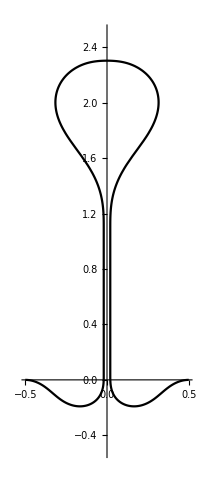

```mathematica
II={10,20,50,80,100,300,340,350,369};
II={369};
For[i=1,i≤Length[II],i++,
Subscript[P, i]=ParametricPlot[{{-x[S],y[S]}/.grs[[II[[i]],6]],{x[S],y[S]}/.grs[[II[[i]],6]]},{S,0,1/2},PlotStyle->{Black,Black}];
];
Show[Table[Subscript[P, k],{k,1,Length[II]}],PlotRange->{{-.5,.5},{-.5,2.5}}]
```

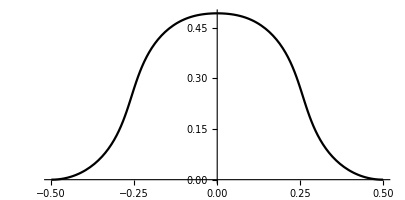

```mathematica
i=10;ParametricPlot[{{-x[S],y[S]}/.grs[[i,6]],{x[S],y[S]}/.grs[[i,6]]},{S,0,1/2},PlotStyle->{Black,Black}]
```

### Heterogeneous stiffness, uniform growth

#### Initial solution, parameters

```mathematica
Clear[γ,R,Sol,sol,EB,px,py];
(* parameters *)
k=50;
dt=0.05;
dth = dt; (* initialising successful step size *)
δ=0.1;
L=1;
η=1;
γ[S_]=1+dt;
px[S_]:=S;
py[S_]:=0;
EB[s_]:=1-.5Exp[-s^2/(.005)];
Sol=FindRoot[RodOde[R],{R,{-42,0.1,-4}}];
Plot[EB[s],{s,0,1/2},PlotRange->{0,1}]
ParametricPlot[Evaluate[{x[S],y[S]}/.EquilSol[R/.Sol]],{S,0,L/2}]
```

-Graphics-

-Graphics-

#### Growth to contact

```mathematica
grs={};
(* first step *)
g=1+dt;
γ[S_]=g;
Sol=FindRoot[RodOde[R],{R,R/.Sol}];
sol=EquilSol[R/.Sol];
rs=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];

(* second step *)
g=g+dt;
γ[s_]=g;
Sol=FindRoot[RodOde[R],{R,R/.Sol}];
sol=EquilSol[R/.Sol];
re=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];

(* tracing *)
flag=0;
FailCount=0;
TOL=10^-6;
MaxDt=0.35;
MaxFails=60;

P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];
P2=Plot[(x[S]-δ)/.sol,{S,0,L/2}];

J1 = CreateWindow[DocumentNotebook[P1],WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
J2 = CreateWindow[DocumentNotebook[P2],WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];

(*Dynamic[Refresh[Show[P,PlotRange->All],UpdateInterval->$TimeUnit,TrackedSymbols->{P}],SynchronousUpdating->True]*)

While[flag==0,
t = (re - rs);
g=g+dt;
γ[s_]=g;
Sol=Quiet[Reap[FindRoot[RodOde[R],{R,re+dt/dth*t}, StepMonitor :> Sow[R]]]];
Err=Norm[RodOde[R/.Sol[[1]]]];
If[Err > TOL, 
(* reject solution, decrease step size *)
FailCount = FailCount + 1; 
g=g-dt;
γ[s_]=g;
dt = 0.5 dt; Print[dt];If[FailCount == MaxFails, flag = 1,];,

(* else accept solution, store data, update foundation *)
sol=EquilSol[R/.Sol[[1]]];
rs = re;
re = R/.Sol[[1]];
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];

Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* update successful step size *)
dth=dt;

(* live plotting *)
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];
P2=Plot[(x[S]-δ)/.sol,{S,0,L/2}];
CreateWindow[DocumentNotebook[P1],J1,WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
 CreateWindow[DocumentNotebook[P2],J2,WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];
(*FinishDynamic[]*);

(* criteria to increase step size, based on number of steps to convergence of FindRoot *)steps = Length[Sol[[2]][[1]]];
If[steps < 4, dt = Min[1.25*dt, MaxDt]; Print[dt],];
];

];
```

0.0625

0.078125

0.0976563

0.12207

0.152588

0.190735

$Aborted

```mathematica
NotebookClose[J1];NotebookClose[J2];
```

```mathematica
Manipulate[ParametricPlot[{x[s],y[s]}/.grs[[i,6]],{s,0,grs[[i,2]]/2},PlotRange->All],{i,1,Length[grs],1}]
```

```mathematica
Manipulate[Plot[(x[s]-δ)/.grs[[i,6]],{s,0,L/2}],{i,1,Length[grs],1}]
```

```mathematica
Save[ToString[$HomeDirectory]<>"/Dropbox/Research (unshared,current)/Morphorods/SelfContact/Lagrangian", grs]
```

#### First contact point

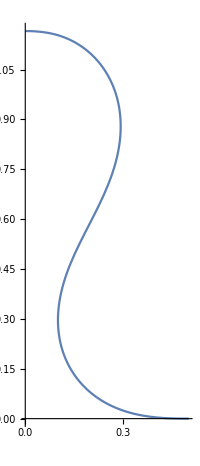

```mathematica
ii=24;
sc=0.33; (* guess for contact location *)
grs=Table[grs[[k]],{k,1,ii}];
γ[S_]=grs[[ii,1]];
R0=grs[[ii,5]];
R0=Flatten[AppendTo[R0,{sc,0}]];
px=grs[[ii,7]];
py=grs[[ii,8]];
Sol=FindRoot[RodOdeContactPt[R],{R,R0}];
sol=EquilSolnContactPt[R/.Sol];
ParametricPlot[{x[S],y[S]}/.sol,{S,0,L/2}]
```

```mathematica
A0=-NIntegrate[x[S]y'[S]/.sol,{S,0,(R/.Sol)[[4]]}]
```

0.182148

```mathematica
rs=Flatten[AppendTo[R/.Sol,0]]
```

Set::write: Tag ReplaceAll in R/.{R→{-7.61589,1.16567,-3.98773,0.328367,0.297195}} is Protected.

{-7.61589,1.16567,-3.98773,0.328367,0.297195,0}

```mathematica
Sol=FindRoot[RodOdeContactPtAreaCons[R],{R,rs}];
sol=EquilSolnContactPtAreaCons[R/.Sol];
```

```mathematica
g=γ[S]
```

3.29105

#### Evolving contact point; Seeking contact region

```mathematica
(* first step done above *)
(*g=3.825;*)
γ[S_]=g;
rs=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* second step *)
dt=0.005;
dth=dt; (* initialising successful dt *)
g=g+dt;
γ[S_]=g;
Sol=FindRoot[RodOdeContactPtAreaCons[R],{R,R/.Sol}];
sol=EquilSolnContactPtAreaCons[R/.Sol];
re=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,re,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* tracing *)
flag=0;
FailCount=0;
TOL=10^-4;
MaxDt=0.1;

P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];
P2=Plot[m[S]/.sol,{S,0,L/2}];

J1 = CreateWindow[DocumentNotebook[P1],WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
J2 = CreateWindow[DocumentNotebook[P2],WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];

(*Dynamic[Refresh[Show[P,PlotRange->All],UpdateInterval->$TimeUnit,TrackedSymbols->{P}],SynchronousUpdating->True]*)

While[flag==0,
t = (re - rs);
g=g+dt;
γ[S_]=g;

Sol=Quiet[Reap[FindRoot[RodOdeContactPtAreaCons[R],{R,re+dt/dth t}, StepMonitor :> Sow[R]]]];
Err=Norm[RodOdeContactPtAreaCons[R/.Sol[[1]]]];
If[Err > TOL, 
(* reject solution, decrease step size *)
FailCount = FailCount + 1; 
g=g-dt;
dt = 0.5 dt; Print[dt];If[FailCount == 100, flag = 1,];,

(* else accept solution, store data, update foundation *)
sol=EquilSolnContactPtAreaCons[R/.Sol[[1]]];
rs = re;
re = R/.Sol[[1]];
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* update successful step size *)
dth=dt;

(* live plotting *)
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol],{S,0,L/2}];
P2=Plot[m[S]/.sol,{S,0,L/2}];
 CreateWindow[DocumentNotebook[P1],J1,WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
 CreateWindow[DocumentNotebook[P2],J2,WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];
(*FinishDynamic[]*)

(* criteria to increase step size, based on number of steps to convergence of FindRoot *)steps = Length[Sol[[2]][[1]]];
If[steps < 4, dt = Min[1.25*dt, MaxDt]; Print[dt],];
];

];
```

$Aborted

```mathematica
NotebookClose[J1];NotebookClose[J2];
```

```mathematica
ii=27;
```

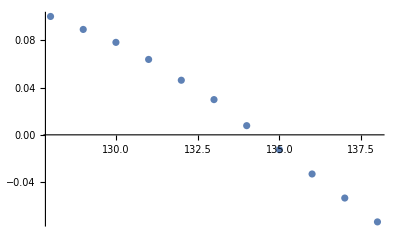

```mathematica
ListPlot[Table[{i,m[S]/.grs[[i,6]]/.S->grs[[i,5,4]]},{i,128,Length[grs]}]]
```

```mathematica
Save[ToString[$HomeDirectory]<>"/Dropbox/Research (unshared,current)/Morphorods/SelfContact/Lagrangian", grs]
```

```mathematica
grs=Get[ToString[$HomeDirectory]<>"/Dropbox/Research (unshared,current)/Morphorods/SelfContact/Lagrangian"];
```

```mathematica
Manipulate[ParametricPlot[{{-x[S],y[S]}/.grs[[i,6]],{x[S],y[S]}/.grs[[i,6]]},{S,0,L/2},PlotRange->All,PlotStyle->{Blue,Blue}],{i,1,Length[grs],1}]
Manipulate[Plot[m[S]/.grs[[i,6]],{S,0,L/2}],{i,1,Length[grs],1}]
```

#### First contact region solution

```mathematica
Length[grs]
```

225

```mathematica
ii=135;
m[S]/.grs[[ii,6]]/.S->grs[[ii,5,4]]
grs=Table[grs[[k]],{k,1,ii}];
```

-0.0125873

```mathematica
A0
```

0.206189

```mathematica
(*A0=0.20618879019655859;*)
γ[S_]=grs[[ii,1]];
px=grs[[ii,7]];
py=grs[[ii,8]];
R0=grs[[ii,5]];
eps=0.01;
R0={R0[[1]],R0[[2]],R0[[3]],R0[[4]]-eps,R0[[4]]+eps,R0[[5]]/2/eps,R0[[6]]};
```

```mathematica
RodOdeContactRegion[R0]
```

{0.000623752,-0.00682961,0.29876,-0.00319619,-0.00919894,-0.00487466,0.0505482}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

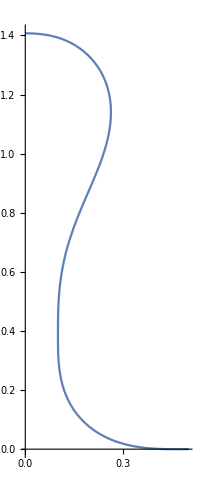

```mathematica
Sol=FindRoot[RodOdeContactRegion[R],{R,R0},AccuracyGoal->6,MaxIterations->Infinity,PrecisionGoal->6];
sol=EquilSolContactRegion[R/.Sol];
ParametricPlot[{x[S],y[S]}/.sol,{S,0,L/2}]
```

```mathematica
Norm[RodOdeContactRegion[R/.Sol]]
```

0.0000765583

```mathematica
R/.Sol
```

{-17.1415,1.40709,-4.61163,0.32312,0.323583,57983.4,-98.3801}

```mathematica
g=γ[S]
```

3.71439

#### Contact region

```mathematica
γ[S_]=g;
rs=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* second step *)
dt=0.001;
dth=dt; (* initialising successful dt *)
g=g+dt;
γ[S_]=g;
Sol=FindRoot[RodOdeContactRegion[R],{R,R/.Sol}];
sol=EquilSolContactRegion[R/.Sol];
re=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,re,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];

(* tracing *)
flag=0;
FailCount=0;
TOL=10^-4;
MaxDt=0.15;

P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];

J1 = CreateWindow[DocumentNotebook[P1],WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];

(*Dynamic[Refresh[Show[P,PlotRange->All],UpdateInterval->$TimeUnit,TrackedSymbols->{P}],SynchronousUpdating->True]*)

While[flag==0,
t = (re - rs);
g=g+dt;
γ[S_]=g;

Sol=Quiet[Reap[FindRoot[RodOdeContactRegion[R],{R,re+dt/dth t}, StepMonitor :> Sow[R]]]];
Err=Norm[RodOdeContactRegion[R/.Sol[[1]]]];
If[Err > TOL, 
(* reject solution, decrease step size *)
FailCount = FailCount + 1; 
g=g-dt;
dt = 0.5 dt; Print[dt];If[FailCount == 200, flag = 1,];,

(* else accept solution, store data, update foundation *)
sol=EquilSolContactRegion[R/.Sol[[1]]];
rs = re;
re = R/.Sol[[1]];
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* update successful step size *)
dth=dt;

(* live plotting *)
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol],{S,0,L/2}];
CreateWindow[DocumentNotebook[P1],J1,WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
 
(* criteria to increase step size, based on number of steps to convergence of FindRoot *)steps = Length[Sol[[2]][[1]]];
If[steps < 4, dt = Min[1.25*dt, MaxDt]; Print[dt],];
];

];
```

$Aborted

```mathematica
NotebookClose[J1]
```

```mathematica
Length[grs]
```

343

```mathematica
Length[grs]
```

343

```mathematica
II={2,10,18,50,260,300,325,343};
For[i=1,i≤Length[II],i++,
Subscript[P, i]=ParametricPlot[{{-x[S],y[S]}/.grs[[II[[i]],6]],{x[S],y[S]}/.grs[[II[[i]],6]]},{S,0,1/2},PlotStyle->{Black,Black}];
];
```

```mathematica
Show[Table[Subscript[P, k],{k,1,Length[II]}],PlotRange->{{-.5,.5},{-.5,3}},AspectRatio->8,ImageSize->80]
```

-Graphics-

```mathematica
Grs=Table[grs[[II[[i]]]],{i,1,Length[II]}];
```

```mathematica
Save[ToString[$HomeDirectory]<>"/Dropbox/Research (unshared,current)/Morphorods/SelfContact/Lagrangian2", Grs]
```

```mathematica
Grs=Get[ToString[$HomeDirectory]<>"/Dropbox/Research (unshared,current)/Morphorods/SelfContact/Lagrangian"];
```

```mathematica
Manipulate[ParametricPlot[{{-x[S],y[S]}/.Grs[[i,6]],{x[S],y[S]}/.Grs[[i,6]]},{S,0,1/2},PlotRange->{{-1,1},{-1,3}},AspectRatio->5],{i,1,Length[Grs],1}]
```

### Heterogeneous stiffness, homogeneous growth, horizontal repulsion

-Graphics-

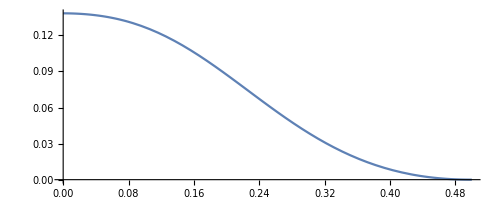

```mathematica
Clear[γ,R,Sol,sol,EB,px,py];
(* parameters *)
k=50;
dt=0.05;
dth = dt; (* initialising successful step size *)
δ=0.025;
L=1;
η=1;
γ[S_]=1+dt;
px[S_]:=S;
py[S_]:=0;
Q = 10.0;
n= 2.0;
EB[s_]:=1-.5Exp[-s^2/(.005)];
Sol=FindRoot[RodOdeRepulsion[R],{R,{-42,0.1,-4}}];
Plot[EB[s],{s,0,1/2},PlotRange->{0,1}]
ParametricPlot[Evaluate[{x[S],y[S]}/.EquilSolRepulsion[R/.Sol]],{S,0,L/2}]
```

#### Growth to self-contact

```mathematica
grs={};
(* first step *)
g=1+dt;
γ[S_]=g;
Sol=FindRoot[RodOdeRepulsion[R],{R,R/.Sol}];
sol=EquilSolRepulsion[R/.Sol];
rs=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];

(* second step *)
g=g+dt;
γ[s_]=g;
Sol=FindRoot[RodOdeRepulsion[R],{R,R/.Sol}];
sol=EquilSolRepulsion[R/.Sol];
re=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];

(* tracing *)
flag=0;
FailCount=0;
TOL=10^-6;
MaxDt=0.35;
MaxFails=60;

P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];
P2=Plot[(x[S]-δ)/.sol,{S,0,L/2}];

J1 = CreateWindow[DocumentNotebook[P1],WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
J2 = CreateWindow[DocumentNotebook[P2],WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];

(*Dynamic[Refresh[Show[P,PlotRange->All],UpdateInterval->$TimeUnit,TrackedSymbols->{P}],SynchronousUpdating->True]*)
rd
While[flag==0,
t = (re - rs);
g=g+dt;
γ[s_]=g;
Sol=Quiet[Reap[FindRoot[RodOdeRepulsion[R],{R,re+dt/dth*t}, StepMonitor :> Sow[R]]]];
Err=Norm[RodOdeRepulsion[R/.Sol[[1]]]];
If[Err > TOL, 
(* reject solution, decrease step size *)
FailCount = FailCount + 1; 
g=g-dt;
γ[s_]=g;
dt = 0.5 dt; Print[dt];If[FailCount == MaxFails, flag = 1,];,

(* else accept solution, store data, update foundation *)
sol=EquilSolRepulsion[R/.Sol[[1]]];
rs = re;
re = R/.Sol[[1]];
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];

Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* update successful step size *)
dth=dt;

(* live plotting *)
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];
P2=Plot[(x[S]-δ)/.sol,{S,0,L/2}];
CreateWindow[DocumentNotebook[P1],J1,WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
 CreateWindow[DocumentNotebook[P2],J2,WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];
(*FinishDynamic[]*);

(* criteria to increase step size, based on number of steps to convergence of FindRoot *)steps = Length[Sol[[2]][[1]]];
If[steps < 4, dt = Min[1.25*dt, MaxDt]; Print[dt],];
];

];
```

rd

0.0625

0.078125

0.0976563

0.12207

0.0610352

$Aborted

```mathematica
NotebookClose[J1];NotebookClose[J2];
```

```mathematica
Manipulate[ParametricPlot[{x[s],y[s]}/.grs[[i,6]],{s,0,grs[[i,2]]/2},PlotRange->All],{i,1,Length[grs],1}]
```

Part::partd: Part specification grs ⟦ 23, 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value 1/2\ grs ⟦ 23, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$89, 2 ⟧} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 23, 2 ⟧ is longer than depth of object.

ParametricPlot::plln: Limiting value 1/2\ grs ⟦ 23, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$89, 2 ⟧} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 23, 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value 1/2\ grs ⟦ 23, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$89, 2 ⟧} is not a machine-sized real number.

Part::partw: Part 23 of {{(1 + 0.05\ ⅇ^-6.25\ Power[« 2 »])^2[S], 1, 1, 868.056, rs, sol, px, py}} does not exist.

Part::partw: Part 23 of {{(1.  + 0.05\ 2.71828^-6.25\ Power[« 2 »])^2[S], 1., 1., 868.056, rs, sol, px, py}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ParametricPlot::plln: Limiting value 1/2\ {{(1 + 0.05\ Power[« 2 »])^2[S], 1, 1, 868.056, rs, sol, px, py}} ⟦ 23, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$89, 2 ⟧} is not a machine-sized real number.

Part::partw: Part 23 of {1 + 0.05` ⅇ^-39.0625` S^2, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, « 1 », {{0.03436278249570261`, 0.`}, {0.03196757607716958`, -0.07589878150860022`}, {0.026902738417898357`, -0.1185170072048991`}, {0.020068476474868584`, -0.13486663229980686`}, {0.012756060608479258`, -0.12414822120927134`}, « 1 », {0.0009484620927244481`, -0.030547182608392037`}, {-0.000027791672536957957`, -0.0032992829045550578`}, {-3.6090495494371057`*^-7, 0.00030019591840245484`}, {-4.4911039848960234`*^-15, 3.9013766223762537`*^-13}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ParametricPlot::plln: Limiting value 1 in {s, 0, 1/2\ grs ⟦ FE`i$$511, 2 ⟧} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 23, 2 ⟧ is longer than depth of object.

ParametricPlot::plln: Limiting value 1/2\ grs ⟦ 23, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$511, 2 ⟧} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 23, 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value 1/2\ grs ⟦ 23, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$181, 2 ⟧} is not a machine-sized real number.

```mathematica
Manipulate[Plot[{x[s]-δ}/.grs[[i,6]],{s,0,grs[[i,2]]/2},PlotRange->All],{i,1,Length[grs],1}]
```

Part::partd: Part specification grs ⟦ 23, 2 ⟧ is longer than depth of object.

Plot::plln: Limiting value 1/2\ grs ⟦ 23, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$91, 2 ⟧} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 23, 2 ⟧ is longer than depth of object.

Plot::plln: Limiting value 1/2\ grs ⟦ 23, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$91, 2 ⟧} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 23, 2 ⟧ is longer than depth of object.

Plot::plln: Limiting value 1/2\ grs ⟦ 23, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$91, 2 ⟧} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 23, 2 ⟧ is longer than depth of object.

Plot::plln: Limiting value 1/2\ grs ⟦ 23, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$91, 2 ⟧} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 23, 2 ⟧ is longer than depth of object.

Plot::plln: Limiting value 1/2\ grs ⟦ 23, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$91, 2 ⟧} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 23, 2 ⟧ is longer than depth of object.

Plot::plln: Limiting value 1/2\ grs ⟦ 23, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$91, 2 ⟧} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 23, 2 ⟧ is longer than depth of object.

Plot::plln: Limiting value 1/2\ grs ⟦ 23, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$91, 2 ⟧} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 23, 2 ⟧ is longer than depth of object.

Plot::plln: Limiting value 1/2\ grs ⟦ 23, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$91, 2 ⟧} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 23, 2 ⟧ is longer than depth of object.

Plot::plln: Limiting value 1/2\ grs ⟦ 23, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$91, 2 ⟧} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 23, 2 ⟧ is longer than depth of object.

Plot::plln: Limiting value 1/2\ grs ⟦ 23, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$91, 2 ⟧} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 23, 2 ⟧ is longer than depth of object.

Plot::plln: Limiting value 1/2\ grs ⟦ 23, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$91, 2 ⟧} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 23, 2 ⟧ is longer than depth of object.

Plot::plln: Limiting value 1/2\ grs ⟦ 23, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$91, 2 ⟧} is not a machine-sized real number.

Part::partw: Part 23 of {{(1 + 0.05\ ⅇ^-6.25\ Power[« 2 »])^2[S], 1, 1, 868.056, rs, sol, px, py}} does not exist.

Part::partw: Part 23 of {{(1.  + 0.05\ 2.71828^-6.25\ Power[« 2 »])^2[S], 1., 1., 868.056, rs, sol, px, py}} does not exist.

Plot::plln: Limiting value 1/2\ {{(1 + 0.05\ Power[« 2 »])^2[S], 1, 1, 868.056, rs, sol, px, py}} ⟦ 23, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$91, 2 ⟧} is not a machine-sized real number.

Part::partw: Part 23 of {{(1 + 0.05\ ⅇ^-6.25\ Power[« 2 »])^2[S], 1, 1, 868.056, rs, sol, px, py}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Plot::plln: Limiting value 1/2\ {{(1 + 0.05\ Power[« 2 »])^2[S], 1, 1, 868.056, rs, sol, px, py}} ⟦ 23, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$91, 2 ⟧} is not a machine-sized real number.

Part::partw: Part 23 of {1 + 0.05` ⅇ^-39.0625` S^2, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, « 1 », {{0.03436278249570261`, 0.`}, {0.03196757607716958`, -0.07589878150860022`}, {0.026902738417898357`, -0.1185170072048991`}, {0.020068476474868584`, -0.13486663229980686`}, {0.012756060608479258`, -0.12414822120927134`}, « 1 », {0.0009484620927244481`, -0.030547182608392037`}, {-0.000027791672536957957`, -0.0032992829045550578`}, {-3.6090495494371057`*^-7, 0.00030019591840245484`}, {-4.4911039848960234`*^-15, 3.9013766223762537`*^-13}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

Part::partw: Part 23 of {1.`  + 0.05` 2.718281828459045`^-39.0625` S^2, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, « 1 », {Developer`PackedArrayForm, {0, 2, « 8 », 20}, {0.03436278249570261`, 0.`, 0.03196757607716958`, -0.07589878150860022`, 0.026902738417898357`, -0.1185170072048991`, 0.020068476474868584`, -0.13486663229980686`, « 4 », 0.0009484620927244481`, -0.030547182608392037`, -0.000027791672536957957`, -0.0032992829045550578`, -3.6090495494371057`*^-7, 0.00030019591840245484`, -4.4911039848960234`*^-15, 3.9013766223762537`*^-13}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Plot::plln: Limiting value 1 in {s, 0, 1/2\ grs ⟦ FE`i$$513, 2 ⟧} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 23, 2 ⟧ is longer than depth of object.

Plot::plln: Limiting value 1/2\ grs ⟦ 23, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$513, 2 ⟧} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 23, 2 ⟧ is longer than depth of object.

Plot::plln: Limiting value 1/2\ grs ⟦ 23, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$513, 2 ⟧} is not a machine-sized real number.

```mathematica
dth
```

0.152588

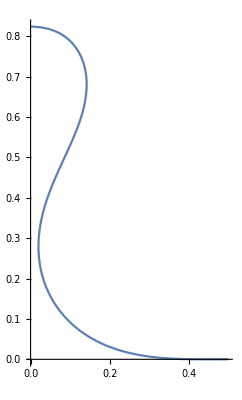

```mathematica
ii=23;
sc=0.26; (* guess for contact location *)
grs=Table[grs[[k]],{k,1,ii}];
γ[S_]=grs[[ii,1]];
R0=grs[[ii,5]];
R0=Flatten[AppendTo[R0,{sc,0}]];
px=grs[[ii,7]];
py=grs[[ii,8]];
Sol=FindRoot[RodOdeContactPtRepulsion[R],{R,R0}];
sol=EquilSolnContactPtRepulsion[R/.Sol];
ParametricPlot[{x[S],y[S]}/.sol,{S,0,L/2}]
```

```mathematica
ii
```

23

```mathematica
g=γ[S]
```

2.56328

### Seeking contact region

```mathematica
g=γ[S];
rs=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* second step *)
dt=0.05;
dth=dt; (* initialising successful dt *)
g=g+dt;
γ[S_]=g;
Sol=FindRoot[RodOdeContactPtRepulsion[R],{R,R/.Sol}];
sol=EquilSolnContactPtRepulsion[R/.Sol];
re=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,re,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* tracing *)
flag=0;
FailCount=0;
TOL=10^-4;
MaxDt=0.15;

P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];
P2=Plot[m[S]/.sol,{S,0,L/2}];

J1 = CreateWindow[DocumentNotebook[P1],WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
J2 = CreateWindow[DocumentNotebook[P2],WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];

(*Dynamic[Refresh[Show[P,PlotRange->All],UpdateInterval->$TimeUnit,TrackedSymbols->{P}],SynchronousUpdating->True]*)

While[flag==0,
t = (re - rs);
g=g+dt;
γ[S_]=g;

Sol=Quiet[Reap[FindRoot[RodOdeContactPtRepulsion[R],{R,re+dt/dth t}, StepMonitor :> Sow[R]]]];
Err=Norm[RodOdeContactPtRepulsion[R/.Sol[[1]]]];
If[Err > TOL, 
(* reject solution, decrease step size *)
FailCount = FailCount + 1; 
g=g-dt;
dt = 0.5 dt; Print[dt];If[FailCount == 100, flag = 1,];,

(* else accept solution, store data, update foundation *)
sol=EquilSolnContactPtRepulsion[ R/.Sol[[1]]];
rs = re;
re = R/.Sol[[1]];
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* update successful step size *)
dth=dt;

(* live plotting *)
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol],{S,0,L/2}];
P2=Plot[m[S]/.sol,{S,0,L/2}];
 CreateWindow[DocumentNotebook[P1],J1,WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
 CreateWindow[DocumentNotebook[P2],J2,WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];
(*FinishDynamic[]*)

(* criteria to increase step size, based on number of steps to convergence of FindRoot *)steps = Length[Sol[[2]][[1]]];
If[steps < 4, dt = Min[1.25*dt, MaxDt]; Print[dt],];
];

];
```

0.0625

0.078125

$Aborted

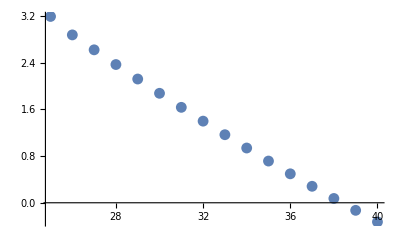

$Aborted

```mathematica
ListPlot[Table[{i,m[S]/.grs[[i,6]]/.S->grs[[i,5,4]]},{i,25,40}]]
```

```mathematica
Manipulate[ParametricPlot[{{-x[S],y[S]}/.grs[[i,6]],{x[S],y[S]}/.grs[[i,6]]},{S,0,L/2},PlotRange->All,PlotStyle->{Blue,Blue}],{i,1,Length[grs],1}]
Manipulate[Plot[m[S]/.grs[[i,6]],{S,0,L/2}],{i,1,Length[grs],1}]
```

Part::partw: Part 41 of {« 1 »} does not exist.

ReplaceAll::reps: {{1.1`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {15}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.046246736367246924`, « 11 », 0.47782956294274`, 0.5`}}, {{0.1816922214795408`, 0.`}, {0.17474847988663905`, -0.29431285861517253`}, {0.16235918711141528`, -0.4649537219610728`}, {0.1430130645932516`, -0.6021615986783576`}, « 7 », {-0.0009156830110004867`, -0.044478516732379555`}, {-0.0012253263388508206`, 0.017839699471462116`}, {-0.0003208757560421681`, 0.025140400000525493`}, {-6.335440731594263`*^-15, 2.9777515689140054`*^-10}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 25 »} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 41 of {« 1 »} does not exist.

ReplaceAll::reps: {{« 1 »} ⟦ 41, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 41 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{1.1`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {15}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.046246736367246924`, « 11 », 0.47782956294274`, 0.5`}}, {{0.1816922214795408`, 0.`}, {0.17474847988663905`, -0.29431285861517253`}, {0.16235918711141528`, -0.4649537219610728`}, {0.1430130645932516`, -0.6021615986783576`}, « 7 », {-0.0009156830110004867`, -0.044478516732379555`}, {-0.0012253263388508206`, 0.017839699471462116`}, {-0.0003208757560421681`, 0.025140400000525493`}, {-6.335440731594263`*^-15, 2.9777515689140054`*^-10}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 25 »} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 26 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partw: Part 26 of {« 1 »} does not exist.

Part::partw: Part 41 of {1.1`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {15}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, « 13 », 0.5`}}, {{0.1816922214795408`, 0.`}, {0.17474847988663905`, -0.29431285861517253`}, {0.16235918711141528`, -0.4649537219610728`}, {0.1430130645932516`, -0.6021615986783576`}, {0.12173053458992128`, -0.6764058618868158`}, « 6 », {-0.0009156830110004867`, -0.044478516732379555`}, {-0.0012253263388508206`, 0.017839699471462116`}, {-0.0003208757560421681`, 0.025140400000525493`}, {-6.335440731594263`*^-15, 2.9777515689140054`*^-10}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 24 »« 1 » does not exist.

ReplaceAll::reps: {{1.1`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {15}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.046246736367246924`, « 11 », 0.47782956294274`, 0.5`}}, {{0.1816922214795408`, 0.`}, {0.17474847988663905`, -0.29431285861517253`}, {0.16235918711141528`, -0.4649537219610728`}, {0.1430130645932516`, -0.6021615986783576`}, « 7 », {-0.0009156830110004867`, -0.044478516732379555`}, {-0.0012253263388508206`, 0.017839699471462116`}, {-0.0003208757560421681`, 0.025140400000525493`}, {-6.335440731594263`*^-15, 2.9777515689140054`*^-10}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 25 »} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 26 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{« 1 »} ⟦ 41, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{1.1`, 1, « 4 », TagBox[« 21 »[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {15}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.046246736367246924`, « 11 », 0.47782956294274`, 0.5`}}, {{0.1816922214795408`, 0.`}, {0.17474847988663905`, -0.29431285861517253`}, {0.16235918711141528`, -0.4649537219610728`}, {0.1430130645932516`, -0.6021615986783576`}, « 7 », {-0.0009156830110004867`, -0.044478516732379555`}, {-0.0012253263388508206`, 0.017839699471462116`}, {-0.0003208757560421681`, 0.025140400000525493`}, {-6.335440731594263`*^-15, 2.9777515689140054`*^-10}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}, « 25 »} ⟦ « 1 » ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 50 of {1.0499999997962273`, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {« 1 »}, {{0.03436278249570261`, 0.`}, {0.03196757607716958`, -0.07589878150860022`}, {0.026902738417898357`, -0.1185170072048991`}, {0.020068476474868584`, -0.13486663229980686`}, {0.012756060608479258`, -0.12414822120927134`}, « 1 », {0.0009484620927244481`, -0.030547182608392037`}, {-0.000027791672536957957`, -0.0032992829045550578`}, {-3.6090495494371057`*^-7, 0.00030019591840245484`}, {-4.4911039848960234`*^-15, 3.9013766223762537`*^-13}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 50 of {1.0499999997962273`, 1.`, « 4 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 0, {11}, {4}, 0, 0, 0, 0, Automatic, {}, {}, False}, « 1 », {Developer`PackedArrayForm, {0, 1, 2, « 7 », 10, 11}, {0.`, 0.051143004552117954`, 0.10174658192472008`, « 6 », 0.4499998594818033`, 0.49999999999999684`}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.`, 0.06089182482681007`, 0.11189504279106804`, 0.16484777875120654`, 0.22041302829215925`, 0.28232020467271113`, 0.368960502530721`, 0.43372506630267005`, 0.4976369442889068`, 0.5`}}, « 1 », {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 50 of {1.0497966415441924`, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, {« 1 »}, {{0.03436278249570261`, 0.`}, {0.03196757607716958`, -0.07589878150860022`}, {0.026902738417898357`, -0.1185170072048991`}, {0.020068476474868584`, -0.13486663229980686`}, {0.012756060608479258`, -0.12414822120927134`}, « 1 », {0.0009484620927244481`, -0.030547182608392037`}, {-0.000027791672536957957`, -0.0032992829045550578`}, {-3.6090495494371057`*^-7, 0.00030019591840245484`}, {-4.4911039848960234`*^-15, 3.9013766223762537`*^-13}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 50, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 50, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 50, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 50, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 50, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ReplaceAll::reps: {grs ⟦ 50, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 1, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 1, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 1, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 1, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 1, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

### Contact along a region

```mathematica
ii=39;
m[S]/.grs[[ii,6]]/.S->grs[[ii,5,4]]
grs=Table[grs[[k]],{k,1,ii}];
```

-0.129697

```mathematica
γ[S_]=grs[[ii,1]];
px=grs[[ii,7]];
py=grs[[ii,8]];
R0=grs[[ii,5]];
eps=0.01;
R0={R0[[1]],R0[[2]],R0[[3]],R0[[4]]-eps,R0[[4]]+eps,R0[[5]]/2/eps};
```

```mathematica
R0
```

{-42.3585,1.15867,-9.06317,0.272194,0.292194,1780.29}

3.7209

```mathematica
RodOdeContactPtRepulsion[R0]
```

{-0.00188179,-0.021442,-0.937592,0.00663964,-3.51851}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

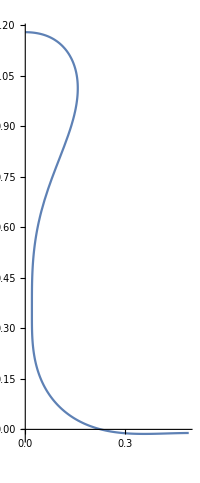

```mathematica
Sol=FindRoot[RodOdeContactRegionRepulsion[R],{R,R0},AccuracyGoal->6,MaxIterations->Infinity,PrecisionGoal->6];
sol=EquilSolContactRegionRepulsion[R/.Sol];
ParametricPlot[{x[S],y[S]}/.sol,{S,0,L/2}]
```

```mathematica
g=γ[S]
```

3.31328

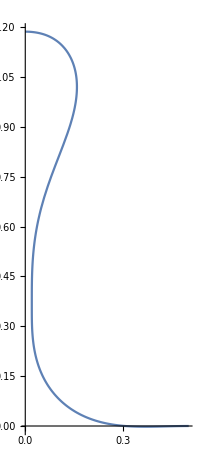

```mathematica
γ[S_]=g;
rs=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* second step *)
dt=0.001;
dth=dt; (* initialising successful dt *)
g=g+dt;
γ[S_]=g;
Sol=FindRoot[RodOdeContactRegionRepulsion[R],{R,R/.Sol}];
sol=EquilSolContactRegionRepulsion[R/.Sol];
re=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,re,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
ParametricPlot[{x[S],y[S]}/.sol,{S,0,L/2}]
```

```mathematica
dth
```

0.001

```mathematica
(* tracing *)
flag=0;
FailCount=0;
TOL=10^-4;
MaxDt=0.15;

P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];

J1 = CreateWindow[DocumentNotebook[P1],WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];

(*Dynamic[Refresh[Show[P,PlotRange->All],UpdateInterval->$TimeUnit,TrackedSymbols->{P}],SynchronousUpdating->True]*)

While[flag==0,
t = (re - rs);
g=g+dt;
γ[S_]=g;

Sol=Quiet[Reap[FindRoot[RodOdeContactRegionRepulsion[R],{R,re+dt/dth t}, StepMonitor :> Sow[R]]]];
Err=Norm[RodOdeContactRegionRepulsion[R/.Sol[[1]]]];
If[Err > TOL, 
(* reject solution, decrease step size *)
FailCount = FailCount + 1; 
g=g-dt;
dt = 0.5 dt; Print[dt];If[FailCount == 200, flag = 1,];,

(* else accept solution, store data, update foundation *)
sol=EquilSolContactRegionRepulsion[R/.Sol[[1]]];
rs = re;
re = R/.Sol[[1]];
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* update successful step size *)
dth=dt;

(* live plotting *)
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol],{S,0,L/2}];
CreateWindow[DocumentNotebook[P1],J1,WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
 
(* criteria to increase step size, based on number of steps to convergence of FindRoot *)steps = Length[Sol[[2]][[1]]];
If[steps < 4, dt = Min[1.25*dt, MaxDt]; Print[dt],];
];

];
```

0.00155575

0.00194469

Part::partw: Part 1 of {} does not exist.

0.00243087

0.00303858

0.00151929

0.000759645

Part::partw: Part 1 of {} does not exist.

0.000949557

0.00118695

0.00148368

0.0018546

0.00231825

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

0.00289782

0.00362227

0.00452784

0.0056598

0.0028299

0.00353737

0.00442172

0.00221086

0.00276357

0.00345447

0.00431808

0.00539761

0.00674701

0.0033735

0.00421688

0.00210844

0.00105422

0.00131777

0.00164722

0.00205902

0.00257378

0.00321722

0.00160861

0.000804306

0.000402153

0.000201076

0.000251346

0.000314182

0.000392727

$Aborted

```mathematica
γ[S]
```

5.06638

```mathematica
dth
```

0.000314182

```mathematica
NotebookClose[J1]
Length[grs]
```

453

```mathematica
II={2,10,18,35, 45, 150, 200, 250, 300, 350, 400, 453};
For[i=1,i≤Length[II],i++,
Subscript[P, i]=ParametricPlot[{{-x[S],y[S]}/.grs[[II[[i]],6]],{x[S],y[S]}/.grs[[II[[i]],6]]},{S,0,1/2},PlotStyle->{Black,Black}];
];
```

```mathematica
Show[Table[Subscript[P, k],{k,1,Length[II]}],PlotRange->{{-.5,.5},{-.5,3}},AspectRatio->8,ImageSize->80]
```

-Graphics-

```mathematica
Grs=Table[grs[[II[[i]]]],{i,1,Length[II]}];
```

```mathematica
Save[ToString[$HomeDirectory]<>"/Documents/MorphoCrypt/Mathematica/SelfContact/", Grs]
```

```mathematica
Manipulate[ParametricPlot[{{-x[S],y[S]}/.Grs[[i,6]],{x[S],y[S]}/.Grs[[i,6]]},{S,0,1/2},PlotRange->{{-1,1},{-1,3}},AspectRatio->5],{i,1,Length[Grs],1}]
```

Part::partd: Part specification Grs ⟦ 7, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {Grs ⟦ 7, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification Grs ⟦ 7, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {Grs ⟦ 7, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification Grs ⟦ 7, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification Grs ⟦ 7, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {Grs ⟦ 7, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification Grs ⟦ 7, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {Grs ⟦ 7, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification Grs ⟦ 7, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification Grs ⟦ 7, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {Grs ⟦ 7, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification Grs ⟦ 7, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {Grs ⟦ 7, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification Grs ⟦ 7, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification Grs ⟦ 7, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {Grs ⟦ 7, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification Grs ⟦ 7, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {Grs ⟦ 7, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification Grs ⟦ 7, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification Grs ⟦ 7, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {Grs ⟦ 7, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification Grs ⟦ 7, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {Grs ⟦ 7, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification Grs ⟦ 7, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification Grs ⟦ 7, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {Grs ⟦ 7, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification Grs ⟦ 7, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {Grs ⟦ 7, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification Grs ⟦ 7, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

### Homogeneous growth, homogeneous stiffness constant area (K = 50)

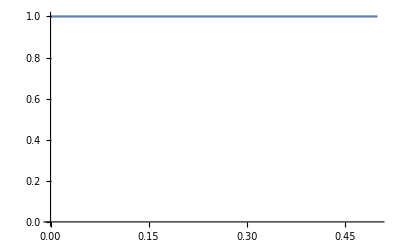

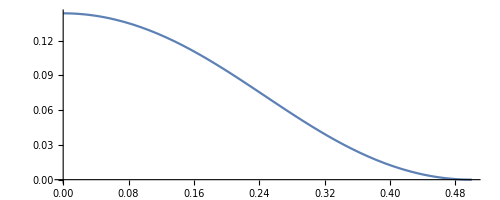

```mathematica
Clear[γ,R,Sol,sol,EB,px,py];
(* parameters *)
k=50;
dt=0.05;
dth = dt; (* initialising successful step size *)
δ=0.02;
L=1;
η=10;
γ[S_]=1+dt;
px[S_]:=S;
py[S_]:=0;
EB[s_]:=1;
Sol=FindRoot[RodOde[R],{R,{-42,0.1,-4}}];
Plot[EB[s],{s,0,1/2},PlotRange->{0,1}]
ParametricPlot[Evaluate[{x[S],y[S]}/.EquilSol[R/.Sol]],{S,0,L/2}]
```

```mathematica
grs={};
(* first step *)
g=1+dt;
γ[S_]=g;
Sol=FindRoot[RodOde[R],{R,R/.Sol}];
sol=EquilSol[R/.Sol];
rs=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];

(* second step *)
g=g+dt;
γ[s_]=g;
Sol=FindRoot[RodOde[R],{R,R/.Sol}];
sol=EquilSol[R/.Sol];
re=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
(* tracing *)
flag=0;
FailCount=0;
TOL=10^-6;
MaxDt=0.35;
MaxFails=60;

P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];
P2=Plot[(x[S]-δ)/.sol,{S,0,L/2}];

J1 = CreateWindow[DocumentNotebook[P1],WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
J2 = CreateWindow[DocumentNotebook[P2],WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];

(*Dynamic[Refresh[Show[P,PlotRange->All],UpdateInterval->$TimeUnit,TrackedSymbols->{P}],SynchronousUpdating->True]*)
rd
While[flag==0,
t = (re - rs);
g=g+dt;
γ[s_]=g;
Sol=Quiet[Reap[FindRoot[RodOde[R],{R,re+dt/dth*t}, StepMonitor :> Sow[R]]]];
Err=Norm[RodOde[R/.Sol[[1]]]];
If[Err > TOL, 
(* reject solution, decrease step size *)
FailCount = FailCount + 1; 
g=g-dt;
γ[s_]=g;
dt = 0.5 dt; Print[dt];If[FailCount == MaxFails, flag = 1,];,

(* else accept solution, store data, update foundation *)
sol=EquilSol[R/.Sol[[1]]];
rs = re;
re = R/.Sol[[1]];
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];

Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* update successful step size *)
dth=dt;

(* live plotting *)
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];
P2=Plot[(x[S]-δ)/.sol,{S,0,L/2}];
CreateWindow[DocumentNotebook[P1],J1,WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
 CreateWindow[DocumentNotebook[P2],J2,WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];
(*FinishDynamic[]*);

(* criteria to increase step size, based on number of steps to convergence of FindRoot *)steps = Length[Sol[[2]][[1]]];
If[steps < 4, dt = Min[1.25*dt, MaxDt]; Print[dt],];
];

];
```

rd

0.0625

0.078125

0.0976563

0.12207

0.152588

$Aborted

```mathematica
NotebookClose[J1];NotebookClose[J2];
```

```mathematica
Manipulate[ParametricPlot[{x[s],y[s]}/.grs[[i,6]],{s,0,grs[[i,2]]/2},PlotRange->All],{i,1,Length[grs],1}]
```

Part::partw: Part 50 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ParametricPlot::plln: Limiting value 1/2\ {« 1 »} ⟦ 50, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$19, 2 ⟧} is not a machine-sized real number.

Part::partw: Part 50 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ParametricPlot::plln: Limiting value 1/2\ {« 1 »} ⟦ 50, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$19, 2 ⟧} is not a machine-sized real number.

Part::partw: Part 42 of {1 + 0.05` ⅇ^-39.0625` S^2, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, « 1 », {{0.03436278249570261`, 0.`}, {0.03196757607716958`, -0.07589878150860022`}, {0.026902738417898357`, -0.1185170072048991`}, {0.020068476474868584`, -0.13486663229980686`}, {0.012756060608479258`, -0.12414822120927134`}, « 1 », {0.0009484620927244481`, -0.030547182608392037`}, {-0.000027791672536957957`, -0.0032992829045550578`}, {-3.6090495494371057`*^-7, 0.00030019591840245484`}, {-4.4911039848960234`*^-15, 3.9013766223762537`*^-13}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ParametricPlot::plln: Limiting value 1 in {s, 0, 1/2\ grs ⟦ FE`i$$521, 2 ⟧} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 42, 2 ⟧ is longer than depth of object.

ParametricPlot::plln: Limiting value 1/2\ grs ⟦ 42, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$521, 2 ⟧} is not a machine-sized real number.

```mathematica
Manipulate[Plot[(x[s]-δ)/.grs[[i,6]],{s,0,L/2}],{i,1,Length[grs],1}]
```

Part::partw: Part 47 of {1 + 0.05` ⅇ^-39.0625` S^2, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, « 1 », {{0.03436278249570261`, 0.`}, {0.03196757607716958`, -0.07589878150860022`}, {0.026902738417898357`, -0.1185170072048991`}, {0.020068476474868584`, -0.13486663229980686`}, {0.012756060608479258`, -0.12414822120927134`}, « 1 », {0.0009484620927244481`, -0.030547182608392037`}, {-0.000027791672536957957`, -0.0032992829045550578`}, {-3.6090495494371057`*^-7, 0.00030019591840245484`}, {-4.4911039848960234`*^-15, 3.9013766223762537`*^-13}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 47 of {1.`  + 0.05` 2.718281828459045`^-39.0625` S^2, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, « 1 », {Developer`PackedArrayForm, {0, 2, « 8 », 20}, {0.03436278249570261`, 0.`, 0.03196757607716958`, -0.07589878150860022`, 0.026902738417898357`, -0.1185170072048991`, 0.020068476474868584`, -0.13486663229980686`, « 4 », 0.0009484620927244481`, -0.030547182608392037`, -0.000027791672536957957`, -0.0032992829045550578`, -3.6090495494371057`*^-7, 0.00030019591840245484`, -4.4911039848960234`*^-15, 3.9013766223762537`*^-13}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 47 of {1 + 0.05` ⅇ^-39.0625` S^2, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, « 1 », {{0.03436278249570261`, 0.`}, {0.03196757607716958`, -0.07589878150860022`}, {0.026902738417898357`, -0.1185170072048991`}, {0.020068476474868584`, -0.13486663229980686`}, {0.012756060608479258`, -0.12414822120927134`}, « 1 », {0.0009484620927244481`, -0.030547182608392037`}, {-0.000027791672536957957`, -0.0032992829045550578`}, {-3.6090495494371057`*^-7, 0.00030019591840245484`}, {-4.4911039848960234`*^-15, 3.9013766223762537`*^-13}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 47, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 47, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 47, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 47, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 47, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ReplaceAll::reps: {grs ⟦ 47, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

```mathematica
(*Save[ToString[$HomeDirectory]<>"/Dropbox/Research (unshared,current)/Morphorods/SelfContact/Lagrangian", grs]*)
```

```mathematica
FindRoot[(θ[S]/.grs[[47, 6]])==-π/2,{S, 0.3}]
```

{S→0.357911}

```mathematica
A0=-NIntegrate[x[S]y'[S]/.grs[[47, 6]],{S,0,(0.357911)}]
```

0.406675

#### First contact point

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

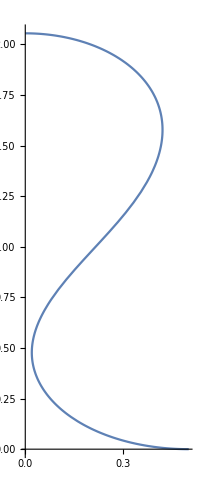

```mathematica
ii=47;
sc=0.358; (* guess for contact location *)
grs=Table[grs[[k]],{k,1,ii}];
γ[S_]=grs[[ii,1]];
R0=grs[[ii,5]];
R0=Flatten[AppendTo[R0,{sc,0, 0}]];
px=grs[[ii,7]];
py=grs[[ii,8]];
Sol=FindRoot[RodOdeContactPtAreaCons[R],{R,R0}];
sol=EquilSolnContactPtAreaCons[R/.Sol];
ParametricPlot[{x[S],y[S]}/.sol,{S,0,L/2}]
```

```mathematica
A0=-NIntegrate[x[S]y'[S]/.sol,{S,0,(R/.Sol)[[4]]}]
```

0.406681

```mathematica
g=γ[S]
```

5.29248

```mathematica
g=γ[S];
rs=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
```

```mathematica
(* second step *)
dt=0.01;
dth=dt; (* initialising successful dt *)
g=g+dt;
γ[S_]=g;
Sol=FindRoot[RodOdeContactPtAreaCons[R],{R,R/.Sol}];
sol=EquilSolnContactPtAreaCons[R/.Sol];
re=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,re,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
(* tracing *)
flag=0;
FailCount=0;
TOL=10^-4;
MaxDt=0.5;

P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];
P2=Plot[m[S]/.sol,{S,0,L/2}];

J1 = CreateWindow[DocumentNotebook[P1],WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
J2 = CreateWindow[DocumentNotebook[P2],WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];

(*Dynamic[Refresh[Show[P,PlotRange->All],UpdateInterval->$TimeUnit,TrackedSymbols->{P}],SynchronousUpdating->True]*)

While[flag==0,
t = (re - rs);
g=g+dt;
γ[S_]=g;

Sol=Quiet[Reap[FindRoot[RodOdeContactPtAreaCons[R],{R,re+dt/dth t}, StepMonitor :> Sow[R]]]];
Err=Norm[RodOdeContactPtAreaCons[R/.Sol[[1]]]];
If[Err > TOL, 
(* reject solution, decrease step size *)
FailCount = FailCount + 1; 
g=g-dt;
dt = 0.5 dt; Print[dt];If[FailCount == 100, flag = 1,];,

(* else accept solution, store data, update foundation *)
sol=EquilSolnContactPtAreaCons[ R/.Sol[[1]]];
rs = re;
re = R/.Sol[[1]];
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* update successful step size *)
dth=dt;

(* live plotting *)
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol],{S,0,L/2}];
P2=Plot[m[S]/.sol,{S,0,L/2}];
 CreateWindow[DocumentNotebook[P1],J1,WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
 CreateWindow[DocumentNotebook[P2],J2,WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];
(*FinishDynamic[]*)

(* criteria to increase step size, based on number of steps to convergence of FindRoot *)steps = Length[Sol[[2]][[1]]];
If[steps < 4, dt = Min[1.25*dt, MaxDt]; Print[dt],];
];

];
```

0.005

0.0025

0.00125

0.000625

0.00078125

0.000390625

0.000195313

0.000244141

0.000305176

0.00038147

0.000476837

0.000596046

0.000298023

0.000372529

0.000465661

0.000582077

0.000727596

0.000909495

0.00113687

0.00142109

0.00177636

0.00222045

0.00277556

0.00138778

0.00173472

0.0021684

0.00271051

0.00338813

0.00423516

0.00529396

0.00264698

0.00330872

0.0041359

0.00206795

0.00103398

0.00129247

0.000646235

0.000807794

0.00100974

0.000504871

0.000252435

0.000315544

0.00039443

0.000493038

0.000616298

0.000308149

0.000154074

0.000192593

0.000240741

0.000120371

0.000150463

0.000188079

0.000235099

0.000293874

0.000146937

0.0000734684

0.0000367342

0.0000459177

0.0000573972

0.0000717465

0.0000896831

0.000112104

0.00014013

0.000175162

0.000218953

0.000273691

0.000342114

0.000427642

Part::partw: Part 1 of {} does not exist.

0.000534553

0.000668191

0.000835239

0.000417619

0.000522024

0.00065253

0.000815663

0.00101958

0.00127447

Part::partw: Part 1 of {} does not exist.

0.00159309

0.00199136

0.00248921

0.00311151

0.00155575

0.000777877

0.000972346

0.00121543

0.00151929

0.00189911

0.00237389

0.00296736

0.00370921

0.00463651

0.00231825

0.00289782

0.00362227

0.00452784

0.0056598

0.00707475

0.00884344

0.0110543

0.00552715

0.00276357

0.00345447

0.00431808

0.00539761

0.00674701

0.00843376

0.0105422

0.0052711

0.00658887

$Aborted

```mathematica
NotebookClose[J1];NotebookClose[J2];
```

```mathematica
Length[grs]
```

591

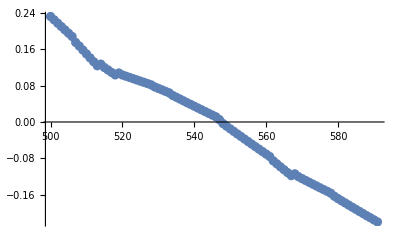

```mathematica
ListPlot[Table[{i,m[S]/.grs[[i,6]]/.S->grs[[i,5,4]]},{i,500, 591}]]
```

```mathematica
ii=560;
m[S]/.grs[[ii,6]]/.S->grs[[ii,5,4]]
grs=Table[grs[[k]],{k,1,ii}];
```

-0.070289

```mathematica
grs[[ii,5]]
```

{-4.6626,2.66708,-2.76178,0.353257,8.1966,-25.0206}

```mathematica
γ[S_]=grs[[ii,1]];
px=grs[[ii,7]];
py=grs[[ii,8]];
R0=grs[[ii,5]];
eps=0.01;
R0={R0[[1]],R0[[2]],R0[[3]],R0[[4]]-eps,R0[[4]]+eps,R0[[5]]/2/eps, R0[[6]]};
```

```mathematica
R0
```

{-4.6626,2.66708,-2.76178,0.343257,0.363257,409.83,-25.0206}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

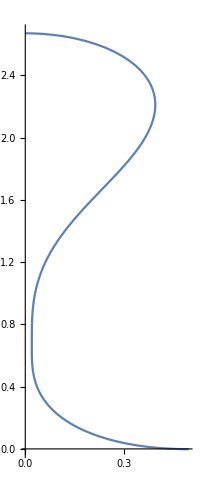

```mathematica
Sol=FindRoot[RodOdeContactRegionAreaCons[R],{R,R0},AccuracyGoal->6,MaxIterations->Infinity,PrecisionGoal->6];
sol=EquilSolContactRegionAreaCons[R/.Sol];
ParametricPlot[{x[S],y[S]}/.sol,{S,0,L/2}]
```

```mathematica
g=γ[S];
rs=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
```

```mathematica
(* second step *)
dt=0.01;
dth=dt; (* initialising successful dt *)
g=g+dt;
γ[S_]=g;
Sol=FindRoot[RodOdeContactRegionAreaCons[R],{R,R/.Sol}];
sol=EquilSolContactRegionAreaCons[R/.Sol];
re=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,re,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
```

```mathematica
(* tracing *)
flag=0;
FailCount=0;
TOL=10^-4;
MaxDt=0.5;

P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];
P2=Plot[m[S]/.sol,{S,0,L/2}];

J1 = CreateWindow[DocumentNotebook[P1],WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
J2 = CreateWindow[DocumentNotebook[P2],WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];

(*Dynamic[Refresh[Show[P,PlotRange->All],UpdateInterval->$TimeUnit,TrackedSymbols->{P}],SynchronousUpdating->True]*)

While[flag==0,
t = (re - rs);
g=g+dt;
γ[S_]=g;

Sol=Quiet[Reap[FindRoot[RodOdeContactRegionAreaCons[R],{R,re+dt/dth t}, StepMonitor :> Sow[R]]]];
Err=Norm[RodOdeContactRegionAreaCons[R/.Sol[[1]]]];
If[Err > TOL, 
(* reject solution, decrease step size *)
FailCount = FailCount + 1; 
g=g-dt;
dt = 0.5 dt; Print[dt];If[FailCount == 100, flag = 1,];,

(* else accept solution, store data, update foundation *)
sol=EquilSolContactRegionAreaCons[ R/.Sol[[1]]];
rs = re;
re = R/.Sol[[1]];
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* update successful step size *)
dth=dt;

(* live plotting *)
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol],{S,0,L/2}];
P2=Plot[m[S]/.sol,{S,0,L/2}];
 CreateWindow[DocumentNotebook[P1],J1,WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
 CreateWindow[DocumentNotebook[P2],J2,WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];
(*FinishDynamic[]*)

(* criteria to increase step size, based on number of steps to convergence of FindRoot *)steps = Length[Sol[[2]][[1]]];
If[steps < 4, dt = Min[1.25*dt, MaxDt]; Print[dt],];
];

];
```

0.005

0.0025

0.00125

0.0015625

0.00195313

0.00244141

0.00305176

0.0038147

0.00476837

0.00596046

0.00745058

0.00931323

0.0116415

0.0145519

0.0181899

0.0227374

0.0284217

0.0355271

0.0444089

0.0222045

$Aborted

```mathematica
II={1,10,18 ,24, 25,30, 31, 35, 38, 39, 45, 47, 157, 158,482, 483, 560, 571, 628, 629,651, 667, 672}
```

{1,10,18,24,25,30,31,35,38,39,45,47,157,158,482,483,560,571,628,629,651,667,672}

```mathematica
GRS=Table[grs[[II[[i]]]],{i, 1, Length[II]}];
```

```mathematica
Table[II[[i]],{i,1, Length[II]}]
```

{1,10,18,24,25,30,31,35,38,39,45,47,157,158,482,483,560,571,628,629,651,667,672}

```mathematica
Length[II]
```

23

```mathematica
Save["~/Documents/MorphoCrypt/Mathematica/Solutions/selfcontactconstantarea_K_50_L_1", GRS];
```

```mathematica
Grs=Get["~/Documents/MorphoCrypt/Mathematica/Solutions/selfcontactconstantarea_K_50_L_1"];
```

```mathematica
Length[Grs]
```

23

### Homogeneous growth, homogeneous stiffness varying repulsion (K = 50)

```mathematica
Q = 15;
n = 2;
```

-Graphics-

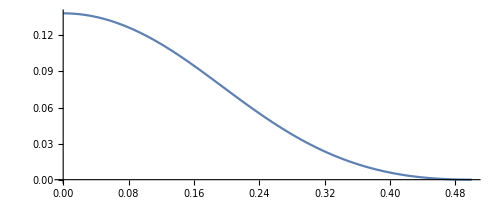

```mathematica
Clear[γ,R,Sol,sol,EB,px,py];
(* parameters *)
k=50;
dt=0.05;
dth = dt; (* initialising successful step size *)
δ=0.02;
L=1;
η=10;
γ[S_]=1+dt;
px[S_]:=S;
py[S_]:=0;
EB[s_]:=1;
Sol=FindRoot[RodOdeRepulsion[R],{R,{-42,0.1,-4}}];
Plot[EB[s],{s,0,1/2},PlotRange->{0,1}]
ParametricPlot[Evaluate[{x[S],y[S]}/.EquilSolRepulsion[R/.Sol]],{S,0,L/2}]
```

```mathematica
grs={};
(* first step *)
g=1+dt;
γ[S_]=g;
Sol=FindRoot[RodOdeRepulsion[R],{R,R/.Sol}];
sol=EquilSolRepulsion[R/.Sol];
rs=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];

(* second step *)
g=g+dt;
γ[s_]=g;
Sol=FindRoot[RodOdeRepulsion[R],{R,R/.Sol}];
sol=EquilSolRepulsion[R/.Sol];
re=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
```

```mathematica
(* tracing *)
flag=0;
FailCount=0;
TOL=10^-6;
MaxDt=0.35;
MaxFails=60;

P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];
P2=Plot[(x[S]-δ)/.sol,{S,0,L/2}];

J1 = CreateWindow[DocumentNotebook[P1],WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
J2 = CreateWindow[DocumentNotebook[P2],WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];

(*Dynamic[Refresh[Show[P,PlotRange->All],UpdateInterval->$TimeUnit,TrackedSymbols->{P}],SynchronousUpdating->True]*)
rd
While[flag==0,
t = (re - rs);
g=g+dt;
γ[s_]=g;
Sol=Quiet[Reap[FindRoot[RodOdeRepulsion[R],{R,re+dt/dth*t}, StepMonitor :> Sow[R]]]];
Err=Norm[RodOdeRepulsion[R/.Sol[[1]]]];
If[Err > TOL, 
(* reject solution, decrease step size *)
FailCount = FailCount + 1; 
g=g-dt;
γ[s_]=g;
dt = 0.5 dt; Print[dt];If[FailCount == MaxFails, flag = 1,];,

(* else accept solution, store data, update foundation *)
sol=EquilSolRepulsion[R/.Sol[[1]]];
rs = re;
re = R/.Sol[[1]];
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];

Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* update successful step size *)
dth=dt;

(* live plotting *)
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];
P2=Plot[(x[S]-δ)/.sol,{S,0,L/2}];
CreateWindow[DocumentNotebook[P1],J1,WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
 CreateWindow[DocumentNotebook[P2],J2,WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];
(*FinishDynamic[]*);

(* criteria to increase step size, based on number of steps to convergence of FindRoot *)steps = Length[Sol[[2]][[1]]];
If[steps < 4, dt = Min[1.25*dt, MaxDt]; Print[dt],];
];

];
```

rd

0.0625

0.078125

0.0976563

$Aborted

```mathematica
NotebookClose[J1];NotebookClose[J2];
```

```mathematica
Manipulate[ParametricPlot[{x[s],y[s]}/.grs[[i,6]],{s,0,grs[[i,2]]/2},PlotRange->All],{i,1,Length[grs],1}]
```

Part::partw: Part 22 of {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ParametricPlot::plln: Limiting value 1/2\ {« 1 »} ⟦ 22, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$30, 2 ⟧} is not a machine-sized real number.

Part::partw: Part 22 of {1 + 0.05` ⅇ^-39.0625` S^2, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, « 1 », {{0.03436278249570261`, 0.`}, {0.03196757607716958`, -0.07589878150860022`}, {0.026902738417898357`, -0.1185170072048991`}, {0.020068476474868584`, -0.13486663229980686`}, {0.012756060608479258`, -0.12414822120927134`}, « 1 », {0.0009484620927244481`, -0.030547182608392037`}, {-0.000027791672536957957`, -0.0032992829045550578`}, {-3.6090495494371057`*^-7, 0.00030019591840245484`}, {-4.4911039848960234`*^-15, 3.9013766223762537`*^-13}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ParametricPlot::plln: Limiting value 1 in {s, 0, 1/2\ grs ⟦ FE`i$$525, 2 ⟧} is not a machine-sized real number.

Part::partw: Part 22 of {1 + 0.05` ⅇ^-39.0625` S^2, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, « 1 », {{0.03436278249570261`, 0.`}, {0.03196757607716958`, -0.07589878150860022`}, {0.026902738417898357`, -0.1185170072048991`}, {0.020068476474868584`, -0.13486663229980686`}, {0.012756060608479258`, -0.12414822120927134`}, « 1 », {0.0009484620927244481`, -0.030547182608392037`}, {-0.000027791672536957957`, -0.0032992829045550578`}, {-3.6090495494371057`*^-7, 0.00030019591840245484`}, {-4.4911039848960234`*^-15, 3.9013766223762537`*^-13}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ParametricPlot::plln: Limiting value 1 in {s, 0, 1/2\ grs ⟦ FE`i$$525, 2 ⟧} is not a machine-sized real number.

Part::partw: Part 22 of {1 + 0.05` ⅇ^-39.0625` S^2, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, « 1 », {{0.03436278249570261`, 0.`}, {0.03196757607716958`, -0.07589878150860022`}, {0.026902738417898357`, -0.1185170072048991`}, {0.020068476474868584`, -0.13486663229980686`}, {0.012756060608479258`, -0.12414822120927134`}, « 1 », {0.0009484620927244481`, -0.030547182608392037`}, {-0.000027791672536957957`, -0.0032992829045550578`}, {-3.6090495494371057`*^-7, 0.00030019591840245484`}, {-4.4911039848960234`*^-15, 3.9013766223762537`*^-13}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ParametricPlot::plln: Limiting value 1 in {s, 0, 1/2\ grs ⟦ FE`i$$525, 2 ⟧} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 22, 2 ⟧ is longer than depth of object.

ParametricPlot::plln: Limiting value 1/2\ grs ⟦ 22, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$525, 2 ⟧} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 22, 2 ⟧ is longer than depth of object.

ParametricPlot::plln: Limiting value 1/2\ grs ⟦ 22, 2 ⟧ in {s, 0, 1/2\ grs ⟦ FE`i$$25, 2 ⟧} is not a machine-sized real number.

```mathematica
Manipulate[Plot[(x[s]-δ)/.grs[[i,6]],{s,0,L/2}],{i,1,Length[grs],1}]
```

Part::partw: Part 21 of {1 + 0.05` ⅇ^-39.0625` S^2, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, « 1 », {{0.03436278249570261`, 0.`}, {0.03196757607716958`, -0.07589878150860022`}, {0.026902738417898357`, -0.1185170072048991`}, {0.020068476474868584`, -0.13486663229980686`}, {0.012756060608479258`, -0.12414822120927134`}, « 1 », {0.0009484620927244481`, -0.030547182608392037`}, {-0.000027791672536957957`, -0.0032992829045550578`}, {-3.6090495494371057`*^-7, 0.00030019591840245484`}, {-4.4911039848960234`*^-15, 3.9013766223762537`*^-13}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 21 of {1.`  + 0.05` 2.718281828459045`^-39.0625` S^2, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, « 1 », {Developer`PackedArrayForm, {0, 2, « 8 », 20}, {0.03436278249570261`, 0.`, 0.03196757607716958`, -0.07589878150860022`, 0.026902738417898357`, -0.1185170072048991`, 0.020068476474868584`, -0.13486663229980686`, « 4 », 0.0009484620927244481`, -0.030547182608392037`, -0.000027791672536957957`, -0.0032992829045550578`, -3.6090495494371057`*^-7, 0.00030019591840245484`, -4.4911039848960234`*^-15, 3.9013766223762537`*^-13}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 21 of {1 + 0.05` ⅇ^-39.0625` S^2, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, « 1 », {{0.03436278249570261`, 0.`}, {0.03196757607716958`, -0.07589878150860022`}, {0.026902738417898357`, -0.1185170072048991`}, {0.020068476474868584`, -0.13486663229980686`}, {0.012756060608479258`, -0.12414822120927134`}, « 1 », {0.0009484620927244481`, -0.030547182608392037`}, {-0.000027791672536957957`, -0.0032992829045550578`}, {-3.6090495494371057`*^-7, 0.00030019591840245484`}, {-4.4911039848960234`*^-15, 3.9013766223762537`*^-13}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 21 of {1 + 0.05` ⅇ^-39.0625` S^2, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, « 1 », {{0.03436278249570261`, 0.`}, {0.03196757607716958`, -0.07589878150860022`}, {0.026902738417898357`, -0.1185170072048991`}, {0.020068476474868584`, -0.13486663229980686`}, {0.012756060608479258`, -0.12414822120927134`}, « 1 », {0.0009484620927244481`, -0.030547182608392037`}, {-0.000027791672536957957`, -0.0032992829045550578`}, {-3.6090495494371057`*^-7, 0.00030019591840245484`}, {-4.4911039848960234`*^-15, 3.9013766223762537`*^-13}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 21 of {1.`  + 0.05` 2.718281828459045`^-39.0625` S^2, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, « 1 », {Developer`PackedArrayForm, {0, 2, « 8 », 20}, {0.03436278249570261`, 0.`, 0.03196757607716958`, -0.07589878150860022`, 0.026902738417898357`, -0.1185170072048991`, 0.020068476474868584`, -0.13486663229980686`, « 4 », 0.0009484620927244481`, -0.030547182608392037`, -0.000027791672536957957`, -0.0032992829045550578`, -3.6090495494371057`*^-7, 0.00030019591840245484`, -4.4911039848960234`*^-15, 3.9013766223762537`*^-13}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 21 of {1 + 0.05` ⅇ^-39.0625` S^2, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, « 1 », {{0.03436278249570261`, 0.`}, {0.03196757607716958`, -0.07589878150860022`}, {0.026902738417898357`, -0.1185170072048991`}, {0.020068476474868584`, -0.13486663229980686`}, {0.012756060608479258`, -0.12414822120927134`}, « 1 », {0.0009484620927244481`, -0.030547182608392037`}, {-0.000027791672536957957`, -0.0032992829045550578`}, {-3.6090495494371057`*^-7, 0.00030019591840245484`}, {-4.4911039848960234`*^-15, 3.9013766223762537`*^-13}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 21 of {1 + 0.05` ⅇ^-39.0625` S^2, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, « 1 », {{0.03436278249570261`, 0.`}, {0.03196757607716958`, -0.07589878150860022`}, {0.026902738417898357`, -0.1185170072048991`}, {0.020068476474868584`, -0.13486663229980686`}, {0.012756060608479258`, -0.12414822120927134`}, « 1 », {0.0009484620927244481`, -0.030547182608392037`}, {-0.000027791672536957957`, -0.0032992829045550578`}, {-3.6090495494371057`*^-7, 0.00030019591840245484`}, {-4.4911039848960234`*^-15, 3.9013766223762537`*^-13}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 21 of {1.`  + 0.05` 2.718281828459045`^-39.0625` S^2, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 7, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, « 1 », {Developer`PackedArrayForm, {0, 2, « 8 », 20}, {0.03436278249570261`, 0.`, 0.03196757607716958`, -0.07589878150860022`, 0.026902738417898357`, -0.1185170072048991`, 0.020068476474868584`, -0.13486663229980686`, « 4 », 0.0009484620927244481`, -0.030547182608392037`, -0.000027791672536957957`, -0.0032992829045550578`, -3.6090495494371057`*^-7, 0.00030019591840245484`, -4.4911039848960234`*^-15, 3.9013766223762537`*^-13}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 21 of {1 + 0.05` ⅇ^-39.0625` S^2, « 6 », TagBox[InterpolatingFunction[{{0.`, 0.5`}}, {4, 3, 1, {10}, {3}, 0, 0, 0, 0, Automatic, {}, {}, False}, « 1 », {{0.03436278249570261`, 0.`}, {0.03196757607716958`, -0.07589878150860022`}, {0.026902738417898357`, -0.1185170072048991`}, {0.020068476474868584`, -0.13486663229980686`}, {0.012756060608479258`, -0.12414822120927134`}, « 1 », {0.0009484620927244481`, -0.030547182608392037`}, {-0.000027791672536957957`, -0.0032992829045550578`}, {-3.6090495494371057`*^-7, 0.00030019591840245484`}, {-4.4911039848960234`*^-15, 3.9013766223762537`*^-13}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]]}« 1 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification grs ⟦ 21, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 21, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 21, 6 ⟧ is longer than depth of object.

ReplaceAll::reps: {grs ⟦ 21, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification grs ⟦ 21, 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ReplaceAll::reps: {grs ⟦ 21, 6 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Plot::plln: Limiting value L/2 in {s, 0, L/2} is not a machine-sized real number.

```mathematica
(*Save[ToString[$HomeDirectory]<>"/Dropbox/Research (unshared,current)/Morphorods/SelfContact/Lagrangian", grs]*)
```

```mathematica
FindRoot[(θ[S]/.grs[[21, 6]])==-π/2,{S, 0.2}]
```

{S→0.229857}

```mathematica
A0=-NIntegrate[x[S]y'[S]/.grs[[24, 6]],{S,0,(0.263681)}]
```

0.0632948

#### First contact point

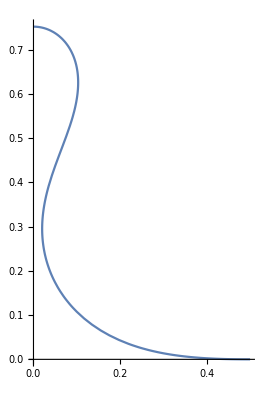

```mathematica
ii=21;
sc=0.2299; (* guess for contact location *)
grs=Table[grs[[k]],{k,1,ii}];
γ[S_]=grs[[ii,1]];
R0=grs[[ii,5]];
(*R0=Flatten[AppendTo[R0,{sc,0}]];*)
R0 = R/.Sol;
px=grs[[ii,7]];
py=grs[[ii,8]];
Sol=FindRoot[RodOdeContactPtRepulsion[R],{R,R0}];
sol=EquilSolnContactPtRepulsion[R/.Sol];
ParametricPlot[{x[S],y[S]}/.sol,{S,0,L/2}]
```

```mathematica
A0=-NIntegrate[x[S]y'[S]/.sol,{S,0,(R/.Sol)[[4]]}]
```

0.085123

```mathematica
g=γ[S]
```

2.31875

```mathematica
g=γ[S];
rs=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
```

```mathematica
(* second step *)
dt=0.05;
dth=dt; (* initialising successful dt *)
g=g+dt;
γ[S_]=g;
Sol=FindRoot[RodOdeContactPtRepulsion[R],{R,R/.Sol}];
sol=EquilSolnContactPtRepulsion[R/.Sol];
re=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,re,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
```

```mathematica
(* tracing *)
flag=0;
FailCount=0;
TOL=10^-4;
MaxDt=0.5;

P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];
P2=Plot[m[S]/.sol,{S,0,L/2}];

J1 = CreateWindow[DocumentNotebook[P1],WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
J2 = CreateWindow[DocumentNotebook[P2],WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];

(*Dynamic[Refresh[Show[P,PlotRange->All],UpdateInterval->$TimeUnit,TrackedSymbols->{P}],SynchronousUpdating->True]*)

While[flag==0,
t = (re - rs);
g=g+dt;
γ[S_]=g;

Sol=Quiet[Reap[FindRoot[RodOdeContactPtRepulsion[R],{R,re+dt/dth t}, StepMonitor :> Sow[R]]]];
Err=Norm[RodOdeContactPtRepulsion[R/.Sol[[1]]]];
If[Err > TOL, 
(* reject solution, decrease step size *)
FailCount = FailCount + 1; 
g=g-dt;
dt = 0.5 dt; Print[dt];If[FailCount == 100, flag = 1,];,

(* else accept solution, store data, update foundation *)
sol=EquilSolnContactPtRepulsion[ R/.Sol[[1]]];
rs = re;
re = R/.Sol[[1]];
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* update successful step size *)
dth=dt;

(* live plotting *)
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol],{S,0,L/2}];
P2=Plot[m[S]/.sol,{S,0,L/2}];
 CreateWindow[DocumentNotebook[P1],J1,WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
 CreateWindow[DocumentNotebook[P2],J2,WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];
(*FinishDynamic[]*)

(* criteria to increase step size, based on number of steps to convergence of FindRoot *)steps = Length[Sol[[2]][[1]]];
If[steps < 4, dt = Min[1.25*dt, MaxDt]; Print[dt],];
];

];
```

$Aborted

```mathematica
NotebookClose[J1];NotebookClose[J2];
```

```mathematica
Length[grs]
```

39

```mathematica
m[S]/.grs[[39, 6]]/.S-> grs[[39, 5, 4]]
```

-0.448642

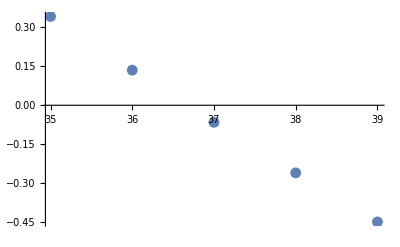

```mathematica
ListPlot[Table[{i,m[S]/.grs[[i,6]]/.S->grs[[i,5,4]]},{i,35, 39}]]
```

```mathematica
ii=37;
m[S]/.grs[[ii,6]]/.S->grs[[ii,5,4]]
grs=Table[grs[[k]],{k,1,ii}];
```

-0.0655538

```mathematica
grs[[ii,5]]
```

{-57.8652,1.02753,-10.5879,0.248204,41.4864}

```mathematica
γ[S_]=grs[[ii,1]];
px=grs[[ii,7]];
py=grs[[ii,8]];
R0=grs[[ii,5]];
eps=0.01;
R0={R0[[1]],R0[[2]],R0[[3]],R0[[4]]-eps,R0[[4]]+eps,R0[[5]]/2/eps};
```

```mathematica
R0
```

{-57.8652,1.02753,-10.5879,0.238204,0.258204,2074.32}

```mathematica
Sol=FindRoot[RodOdeContactRegionRepulsion[R],{R,R0},AccuracyGoal->6,MaxIterations->Infinity,PrecisionGoal->6];
sol=EquilSolContactRegionRepulsion[R/.Sol];
ParametricPlot[{x[S],y[S]}/.sol,{S,0,L/2}]
```

$Aborted

ReplaceAll::reps: {-48.8735, 1.1801, -9.75374, 0.258597, 38.4781} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-48.8735, 1.1801, -9.75374, 0.258593, 38.4766} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 6 of {{-48.8735, 1.1801, -9.75374, 0.258593, 38.4766}, {{R/. {-48.8735, 1.1801, -9.75374, 0.258597, 38.4781}, R/. {-48.8735, 1.1801, -9.75374, 0.258593, 38.4766}, R/. {-48.8735, 1.1801, -9.75374, 0.258593, 38.4766}, R/. {-48.8735, 1.1801, -9.75374, 0.258593, 38.4766}}}} does not exist.

Part::partw: Part 4 of {{-48.8735, 1.1801, -9.75374, 0.258593, 38.4766}, {{R/. {-48.8735, 1.1801, -9.75374, 0.258597, 38.4781}, R/. {-48.8735, 1.1801, -9.75374, 0.258593, 38.4766}, R/. {-48.8735, 1.1801, -9.75374, 0.258593, 38.4766}, R/. {-48.8735, 1.1801, -9.75374, 0.258593, 38.4766}}}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

NDSolve::ndinnt: Initial condition {{-48.8735, 1.1801, -9.75374, 0.258593, 38.4766}, {{R/. {-48.8735, 1.1801, -9.75374, 0.258597, 38.4781}, R/. {-48.8735, 1.1801, -9.75374, 0.258593, 38.4766}, R/. {-48.8735, 1.1801, -9.75374, 0.258593, 38.4766}, R/. {-48.8735, 1.1801, -9.75374, 0.258593, 38.4766}}}} ⟦ 3 ⟧ is not a number or a rectangular array of numbers.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[SuperscriptBox[« 8 »nx[0] == {-48.8735052331505`, 1.1800988212063286`, -9.753740447912095`, 0.2585933866382664`, 38.47661656720845`}ny[0] == 0m[0] == {{-48.8735052331505`, 1.1800988212063286`, -9.753740447912095`, 0.2585933866382664`, 38.47661656720845`}, {{R/. {« 5 »}, R/. {« 5 »}, R/. {« 5 »}, R/. {« 5 »}}}} ⟦ 3 ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[SuperscriptBox[« 8 »nx[0.`] == {-48.8735052331505`, 1.1800988212063286`, -9.753740447912095`, 0.2585933866382664`, 38.47661656720845`}ny[0.`] == 0.`m[0.`] == {{-48.8735052331505`, 1.1800988212063286`, -9.753740447912095`, 0.2585933866382664`, 38.47661656720845`}, {{R/. {« 5 »}, R/. {« 5 »}, R/. {« 5 »}, R/. {« 5 »}}}} ⟦ 3 ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[SuperscriptBox[« 8 »nx[0] == {-48.8735052331505`, 1.1800988212063286`, -9.753740447912095`, 0.2585933866382664`, 38.47661656720845`}ny[0] == 0m[0] == {{-48.8735052331505`, 1.1800988212063286`, -9.753740447912095`, 0.2585933866382664`, 38.47661656720845`}, {{R/. {« 5 »}, R/. {« 5 »}, R/. {« 5 »}, R/. {« 5 »}}}} ⟦ 3 ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-Graphics-

```mathematica
g=γ[S];
rs=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
```

```mathematica
(* second step *)
dt=0.05;
dth=dt; (* initialising successful dt *)
g=g+dt;
γ[S_]=g;
Sol=FindRoot[RodOdeContactRegionRepulsion[R],{R,R/.Sol}];
sol=EquilSolContactRegionRepulsion[R/.Sol];
re=R/.Sol;
AppendTo[grs,{γ[S],L,EB[s],k,re,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
(* tracing *)
dt = 0.05;
flag=0;
FailCount=0;
TOL=10^-4;
MaxDt=0.5;

P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];
P2=Plot[m[S]/.sol,{S,0,L/2}];

J1 = CreateWindow[DocumentNotebook[P1],WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
J2 = CreateWindow[DocumentNotebook[P2],WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];

(*Dynamic[Refresh[Show[P,PlotRange->All],UpdateInterval->$TimeUnit,TrackedSymbols->{P}],SynchronousUpdating->True]*)

While[flag==0,
t = (re - rs);
g=g+dt;
γ[S_]=g;

Sol=Quiet[Reap[FindRoot[RodOdeContactRegionRepulsion[R],{R,re+dt/dth t}, StepMonitor :> Sow[R]]]];
Err=Norm[RodOdeContactRegionRepulsion[R/.Sol[[1]]]];
If[Err > TOL, 
(* reject solution, decrease step size *)
FailCount = FailCount + 1; 
g=g-dt;
dt = 0.5 dt; Print[dt];If[FailCount == 100, flag = 1,];,

(* else accept solution, store data, update foundation *)
sol=EquilSolContactRegionRepulsion[ R/.Sol[[1]]];
rs = re;
re = R/.Sol[[1]];
AppendTo[grs,{γ[S],L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* update successful step size *)
dth=dt;

(* live plotting *)
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol],{S,0,L/2}];
P2=Plot[m[S]/.sol,{S,0,L/2}];
 CreateWindow[DocumentNotebook[P1],J1,WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
 CreateWindow[DocumentNotebook[P2],J2,WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];
(*FinishDynamic[]*)

(* criteria to increase step size, based on number of steps to convergence of FindRoot *)steps = Length[Sol[[2]][[1]]];
If[steps < 4, dt = Min[1.25*dt, MaxDt]; Print[dt],];
];

];
```

0.025

0.0125

0.00625

0.0078125

0.00976563

0.012207

0.0152588

0.00762939

0.00953674

0.0119209

0.00596046

0.00298023

0.00149012

0.000745058

0.000372529

0.000186265

0.000232831

0.000291038

0.000363798

0.000454747

0.000568434

0.000284217

0.000142109

0.0000710543

0.0000355271

0.0000177636

0.0000222045

0.0000277556

0.0000346945

0.0000433681

0.0000542101

0.0000677626

0.0000847033

0.000105879

0.000132349

0.000165436

0.000206795

0.000258494

0.000323117

0.000403897

0.000504871

0.000631089

0.000788861

0.00039443

0.000197215

0.000246519

0.000308149

0.000385186

0.000481482

0.000601853

0.000752316

0.000940395

0.000470198

0.000235099

0.000117549

0.000146937

0.000183671

0.000229589

0.000114794

0.000143493

0.000179366

0.000224208

0.00028026

0.000350325

0.000437906

0.000547382

$Aborted

```mathematica
γ[S]
```

7.60333

```mathematica
Length[grs]
```

417

```mathematica
grs[[230,1]]
```

7.50772

```mathematica
II={1,10, 17,21, 22, 25, 27,28,  32,42, 43,51,52,83,102,135,136,155,156,177,230,417};
Length[II]
```

22

```mathematica
GRS=Table[grs[[II[[i]]]],{i, 1, Length[II]}];
```

```mathematica
Q
```

2.5

```mathematica
Save["~/Documents/MorphoCrypt/Mathematica/Solutions/selfcontactrepulsion_Q_2p5_N_2_K_50_L_1", GRS];
```

```mathematica
Grs=Get["~/Documents/MorphoCrypt/Mathematica/Solutions/selfcontactconstantarea_K_50_L_1"];
```

```mathematica
Length[Grs]
```

23

```mathematica
Grs[[15,1]]
```

5.99553

```mathematica
6-Grs[[15,1]]
```

0.00446852

```mathematica
6-Grs[[16,1]]
```

-0.00119128

```mathematica
S0Values = Range[0, 600, 1]/1200.0;
```

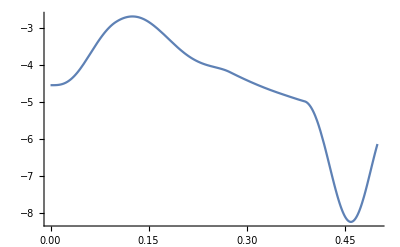

```mathematica
currentsol = Grs[[23,6]];

Plot[(nx[S]*Cos[θ[S]]+ny[S]*Sin[θ[S]])/.currentsol,{S, 0, 1/2}]
```

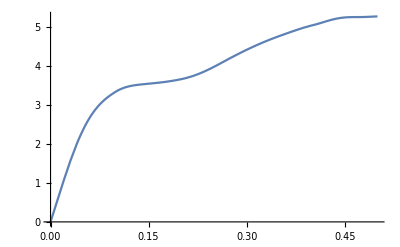

```mathematica
Plot[(ny[S])/.currentsol,{S, 0, 1/2}]
```

```mathematica
evaluatedSol = Table[{S, x[S], y[S],nx[S],ny[S],θ[S],m[S]}/.currentsol/.S-> S0Values[[i]],{i, 1, Length[S0Values]}];
```

```mathematica
Export["~/Documents/MorphoCrypt/Mathematica/Solutions/selfcontactconstantarea_K_50_L_1_T_5_sol.csv", evaluatedSol];
```

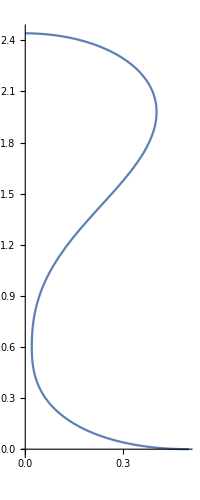

```mathematica
ParametricPlot[{x[S],y[S]}/.currentsol, {S, 0, 0.5}]
```

### Heterogeneous growth, horizontal repulsion, i.e. putting it all together

```mathematica
(* Get the data for the initial solution *)
(*initSolData = Import["~/Documents/MorphoCrypt/Data/planarmorphorodsinextkf0p01L1sol_1"];
y0=initSolData[[300]][[4]];
nx0=initSolData[[300]][[5]];
m0=initSolData[[300]][[8]];
R0 = {nx0, y0,m0}*)
(*R0 = {-42,0.1,-4}(*;*)*)
```

{-98.0767,0.0335096,-0.987072}

```mathematica
R0  = {-42,0.1,-4};
```

First, look at self-contact with the constant area (teardrop shape)

```mathematica
Subscript[σ, w]=0.08
```

0.08

```mathematica
W=Function[s,Exp[-(s/0.16)^2]];
```

```mathematica
(*w = 0.010;
L0=0.125;
h = 0.015;
kf =0.01;
k=(12*kf*L0^4)/(w*h^3);*)
k = 50;
```

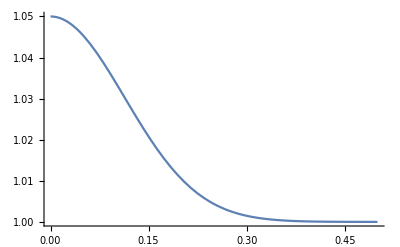

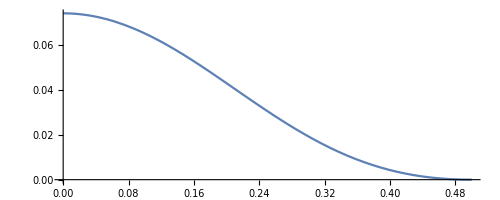

```mathematica
Clear[γ,R,Sol,sol,EB,px,py, γOld, γNew, s];
Q = 10;
n = 2;
dt=0.05;
dth = dt; (* initialising successful step size *)
δ=0.02;
L=1;
η=10;
γ[S_]:=1+dt*W[S];
(*g = 1+dt;*)
(*γ[S_]=g;*)
px[S_]:=S;
py[S_]:=0;
EB[s_]:=1;
Sol=FindRoot[RodOdeRepulsion[R],{R,R0}];
Plot[γ[S0],{S0,0,1/2}]
ParametricPlot[Evaluate[{x[S],y[S]}/.EquilSolRepulsion[R/.Sol]],{S,0,L/2}]
```

```mathematica
Sol
```

{R→{-65.8177,0.074289,-1.88104}}

```mathematica
grs={};
(* first step *)
γ[S_]=1+dt*W[S];
(*g = 1+dt;
γ[S_]= g;*)
Sol=FindRoot[RodOdeRepulsion[R],{R,R/.Sol}];
sol=EquilSolRepulsion[R/.Sol];
rs=R/.Sol;
AppendTo[grs,{γ,L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
```

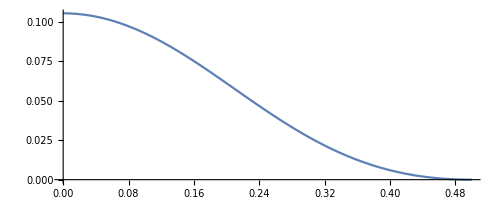

```mathematica
(* second step *)
Clear[γOld,γNew];
γOld=γ;
γNew=FunctionInterpolation[Evaluate[Table[D[γOld[S]*(1+dt*W[s[S]])/.sol,{S,k}],{k, 0, 1}]],{S, 0, 1/2}];

γ=γNew;
(*g=g*(1+dt);*)
(*γ[S_]=g;*)
Sol=FindRoot[RodOdeRepulsion[R],{R,R/.Sol}];
sol=EquilSolRepulsion[R/.Sol];
re=R/.Sol;
AppendTo[grs,{γ,L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]]
```

```mathematica
(* tracing *)
(*dt = 0.075;*)
flag=0;
FailCount=0;
TOL=10^-6;
MaxDt=0.3;
MaxFails=60;
(*
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];*)
P1=Plot[γ[S],{S,0,L/2},PlotRange-> Full];
P2=Plot[(x[S]-δ)/.sol,{S,0,L/2}];

J1 = CreateWindow[DocumentNotebook[P1],WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
J2 = CreateWindow[DocumentNotebook[P2],WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];

(*Dynamic[Refresh[Show[P,PlotRange->All],UpdateInterval->$TimeUnit,TrackedSymbols->{P}],SynchronousUpdating->True]*)
rd
While[flag==0,
t = (re - rs);
γOld=γ;
γNew=FunctionInterpolation[Evaluate[Table[D[γOld[S]*(1+dt*W[s[S]])/.sol,{S,k}],{k, 0, 1}]],{S, 0, 1/2}];

γ=γNew;
(*g=g*(1+dt);
γ[S_]=g;*)
Sol=Quiet[Reap[FindRoot[RodOdeRepulsion[R],{R,re+dt/dth*t}, StepMonitor :> Sow[R],MaxIterations->Infinity]]];
Err=Norm[RodOdeRepulsion[R/.Sol[[1]]]];
If[Err > TOL, 
(* reject solution, decrease step size *)
FailCount = FailCount + 1; 
γ=γOld;
(*g=g/(1+dt);*)
dt = 0.5* dt; Print[dt];If[FailCount == MaxFails, flag = 1,];,

(* else accept solution, store data, update foundation *)
sol=EquilSolRepulsion[R/.Sol[[1]]];
rs = re;
re = R/.Sol[[1]];
AppendTo[grs,{γ,L,EB[s],k,rs,sol,px,py}];

Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* update successful step size *)
dth=dt;

(* live plotting *)
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2},PlotRange-> Full]];
(*P1 = Plot[γ[S],{S, 0, L/2}];*)
P2=Plot[(x[S]-δ)/.sol,{S,0,L/2}];
CreateWindow[DocumentNotebook[P1],J1,WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
 CreateWindow[DocumentNotebook[P2],J2,WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];
(*FinishDynamic[]*);

(* criteria to increase step size, based on number of steps to convergence of FindRoot *)steps = Length[Sol[[2]][[1]]];
If[steps < 4, dt = Min[1.25*dt, MaxDt];];
];

];
```

rd

$Aborted

```mathematica
Length[grs]
```

29

```mathematica
NotebookClose[J1];NotebookClose[J2];
```

```mathematica
Manipulate[ParametricPlot[{x[S],y[S]}/.grs[[i,6]],{S,0,grs[[i,2]]/2},PlotRange->All],{i,1,Length[grs],1}]
```

Part::partd: Part specification grs ⟦ 27, 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value 1/2\ grs ⟦ 27, 2 ⟧ in {S, 0, 1/2\ grs ⟦ FE`i$$15, 2 ⟧} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 27, 2 ⟧ is longer than depth of object.

ParametricPlot::plln: Limiting value 1/2\ grs ⟦ 27, 2 ⟧ in {S, 0, 1/2\ grs ⟦ FE`i$$15, 2 ⟧} is not a machine-sized real number.

```mathematica
Manipulate[Plot[{x[S]-δ}/.grs[[i,6]],{S,0,grs[[i,2]]/2},PlotRange->All],{i,1,Length[grs],1}]
```

Part::partd: Part specification grs ⟦ 1, 2 ⟧ is longer than depth of object.

Plot::plln: Limiting value 1/2\ grs ⟦ 1, 2 ⟧ in {S, 0, 1/2\ grs ⟦ FE`i$$17, 2 ⟧} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 1, 2 ⟧ is longer than depth of object.

Plot::plln: Limiting value 1/2\ grs ⟦ 1, 2 ⟧ in {S, 0, 1/2\ grs ⟦ FE`i$$17, 2 ⟧} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 1, 2 ⟧ is longer than depth of object.

Plot::plln: Limiting value 1/2\ grs ⟦ 1, 2 ⟧ in {S, 0, 1/2\ grs ⟦ FE`i$$17, 2 ⟧} is not a machine-sized real number.

Part::partd: Part specification grs ⟦ 1, 2 ⟧ is longer than depth of object.

Plot::plln: Limiting value 1/2\ grs ⟦ 1, 2 ⟧ in {S, 0, 1/2\ grs ⟦ FE`i$$17, 2 ⟧} is not a machine-sized real number.

```mathematica
FindRoot[((x[S]-δ)/.grs[[27,6]])==0, {S, 0.3}]
```

{S→0.0232348}

```mathematica
A0=-NIntegrate[x[S]y'[S]/.grs[[61,6]],{S,0,0.0325895}]
```

0.0615081

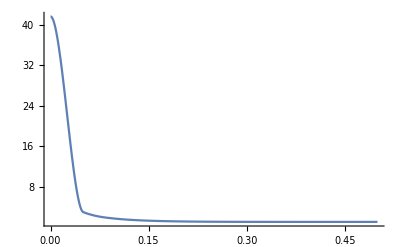

```mathematica
Plot[γOld[S],{S, 0, 0.5},PlotRange-> Full]
```

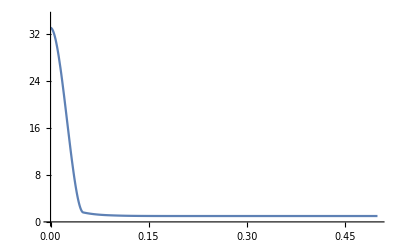

```mathematica
Plot[grs[[79,1]][S],{S, 0, 0.5},PlotRange-> {0, 35}]
```

### First contact point

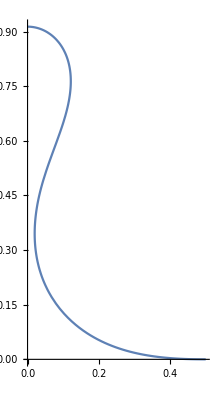

```mathematica
ii=27;
sc=0.023234815142090852; (* guess for contact location *)
grs=Table[grs[[k]],{k,1,ii}];
γ=grs[[ii,1]];
(*γ[S_] = 3.58;*)
R0=grs[[ii,5]];
R0=Flatten[AppendTo[R0,{sc,  0}]];
(*(*R0 = {-3.1327, 1.2074, -3.5601, sc, 0, 1.1849};*)
R0 = {-6.098556586658727,1.2337341341162347,-3.5489434493968615,0.3295597752448023,-2.3737750430278712,5.943708892342442};*)
px=grs[[ii,7]];
py=grs[[ii,8]];
Sol=FindRoot[RodOdeContactPtRepulsion[R],{R,R0}];
sol=EquilSolnContactPtRepulsion[R/.Sol];
ParametricPlot[{x[S],y[S]}/.sol,{S,0,L/2},PlotRange-> All]
```

```mathematica
Sol
```

{R→{-42.228,0.913427,-9.39145,0.03016,3.9726}}

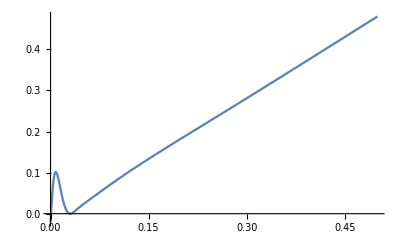

```mathematica
Plot[x[S]-δ/.sol,{S, 0, L/2}]
```

Seeking the contact region solution

```mathematica
rs=R/.Sol;
AppendTo[grs,{γ,L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
```

```mathematica
(* second step *)
dt=0.05;
dth=dt; (* initialising successful dt *)
Clear[γOld,γNew];
γOld=γ;
γNew=FunctionInterpolation[Evaluate[Table[D[γOld[S]*(1+dt*W[s[S]])/.sol,{S,k}],{k, 0, 1}]],{S, 0, 1/2}];

γ=γNew;
Sol=FindRoot[RodOdeContactPtRepulsion[R],{R,R/.Sol}];
sol=EquilSolnContactPtRepulsion[R/.Sol];
re=R/.Sol;
```

```mathematica
AppendTo[grs,{γ,L,EB[s],k,re,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
```

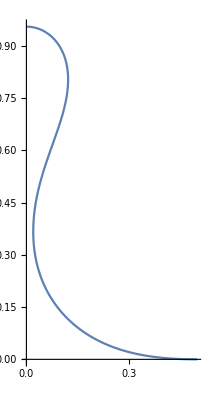

```mathematica
ParametricPlot[{x[S],y[S]}/.sol,{S, 0, L/2},PlotRange-> Full]
```

```mathematica
(* tracing *)
flag=0;
FailCount=0;
TOL=10^-4;
MaxDt=0.5;

P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2},PlotRange-> Full]];
P2=Plot[m[S]/.sol,{S,0,L/2}];

J1 = CreateWindow[DocumentNotebook[P1],WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
J2 = CreateWindow[DocumentNotebook[P2],WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];

(*Dynamic[Refresh[Show[P,PlotRange->All],UpdateInterval->$TimeUnit,TrackedSymbols->{P}],SynchronousUpdating->True]*)

While[flag==0,
t = (re - rs);
Clear[γOld,γNew];
γOld=γ;
γNew=FunctionInterpolation[Evaluate[Table[D[γOld[S]*(1+dt*W[s[S]])/.sol,{S,k}],{k, 0, 1}]],{S, 0, 1/2}];

γ=γNew;
Sol=Quiet[Reap[FindRoot[RodOdeContactPtRepulsion[R],{R,re+dt/dth t}, StepMonitor :> Sow[R]]]];
Err=Norm[RodOdeContactPtRepulsion[R/.Sol[[1]]]];
If[Err > TOL, 
(* reject solution, decrease step size *)
FailCount = FailCount + 1; 
γ=γOld;
dt = 0.5 dt; Print[dt];If[FailCount == 100, flag = 1,];,

(* else accept solution, store data, update foundation *)
sol=EquilSolnContactPtRepulsion[ R/.Sol[[1]]];
rs = re;
re = R/.Sol[[1]];
AppendTo[grs,{γ,L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* update successful step size *)
dth=dt;

(* live plotting *)
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol],{S,0,L/2},PlotRange-> Full];
P2=Plot[m[S]/.sol,{S,0,L/2}];
 CreateWindow[DocumentNotebook[P1],J1,WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
 CreateWindow[DocumentNotebook[P2],J2,WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];
(*FinishDynamic[]*)

(* criteria to increase step size, based on number of steps to convergence of FindRoot *)steps = Length[Sol[[2]][[1]]];
If[steps < 4, dt = Min[1.25*dt, MaxDt]; Print[dt],];
];

];
```

0.0625

$Aborted

```mathematica
Length[grs]
```

38

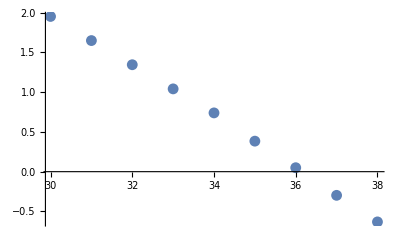

```mathematica
ListPlot[Table[{i,m[S]/.grs[[i,6]]/.S->grs[[i,5,4]]},{i,30, 38}]]
```

```mathematica
ii=37;
m[S]/.grs[[ii,6]]/.S->grs[[ii,5,4]]
```

-0.297887

### First contact region point

```mathematica
ii=37;
m[S]/.grs[[ii,6]]/.S->grs[[ii,5,4]]
grs=Table[grs[[k]],{k,1,ii}];
```

-0.297887

```mathematica
grs[[ii,5]]
```

{-40.0552,1.27126,-8.8021,0.0261371,28.465}

```mathematica
γ=grs[[ii,1]];
px=grs[[ii,7]];
py=grs[[ii,8]];
R0=grs[[ii,5]];
eps=0.005;
R0={R0[[1]],R0[[2]],R0[[3]],R0[[4]]-eps,R0[[4]]+eps,R0[[5]]/2/eps};
```

```mathematica
R0
```

{-57.9934,1.00718,-10.1601,0.0227807,0.0302807,7647.84}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

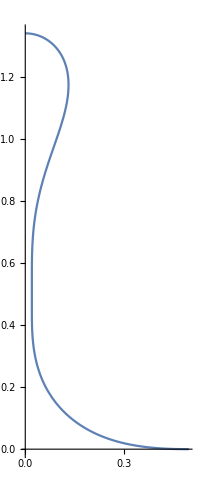

```mathematica
Sol=FindRoot[RodOdeContactRegionRepulsion[R],{R,R/.Sol},MaxIterations-> Infinity];
sol=EquilSolContactRegionRepulsion[R/.Sol];
ParametricPlot[{x[S],y[S]}/.sol,{S,0,L/2},PlotRange-> All]
```

```mathematica
rs=R/.Sol;
AppendTo[grs,{γ,L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
```

```mathematica
rs
```

{-40.0342,1.33885,-8.79478,0.0231494,0.0272908,7620.66}

```mathematica
(* second step *)
(*dt=0.005;
dth = dt;
γ=γOld;
Clear[γOld,γNew];
γOld=γ;
γNew=FunctionInterpolation[Evaluate[Table[D[γOld[S]*(1+dt*W[s[S]])/.sol,{S,k}],{k, 0, 1}]],{S, 0, 1/2}];
γ=γNew;*)
Sol=FindRoot[RodOdeContactRegionRepulsion[R],{R,R/.Sol},MaxIterations->Infinity];
sol=EquilSolContactRegionRepulsion[R/.Sol];
re=R/.Sol;
```

```mathematica
AppendTo[grs,{γ,L,EB[s],k,re,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
```

```mathematica
Save["~/Documents/MorphoCrypt/Mathematica/Solutions/selfcontat_fullmorphology_nu_10_k_50_L_1_current_sigma_2w_Q_10_N_2", grs]
```

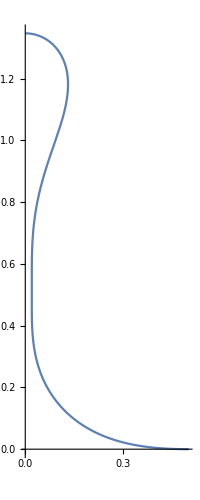

```mathematica
ParametricPlot[{x[S],y[S]}/.sol,{S,0,L/2},PlotRange-> All]
```

```mathematica
dth
```

0.0000371749

```mathematica
(* tracing *)
dt = 0.00005;
flag=0;
FailCount=0;
TOL=10^-4;
MaxDt=0.5;

P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2},PlotRange-> Full]];
P2=Plot[m[S]/.sol,{S,0,L/2}];

J1 = CreateWindow[DocumentNotebook[P1],WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
J2 = CreateWindow[DocumentNotebook[P2],WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];

(*Dynamic[Refresh[Show[P,PlotRange->All],UpdateInterval->$TimeUnit,TrackedSymbols->{P}],SynchronousUpdating->True]*)

While[flag==0,
t = (re - rs);
Clear[γOld,γNew];
γOld=γ;
γNew=FunctionInterpolation[Evaluate[Table[D[γOld[S]*(1+dt*W[s[S]])/.sol,{S,k}],{k, 0, 1}]],{S, 0, 1/2}];

γ=γNew;
Sol=Quiet[Reap[FindRoot[RodOdeContactRegionRepulsion[R],{R,re+dt/dth t},StepMonitor :> Sow[R]]]];
Err=Norm[RodOdeContactRegionRepulsion[R/.Sol[[1]]]];
If[Err > TOL, 
(* reject solution, decrease step size *)
FailCount = FailCount + 1; 
γ=γOld;
dt = 0.75 dt; Print[dt];If[FailCount == 100, flag = 1,];,

(* else accept solution, store data, update foundation *)
sol=EquilSolContactRegionRepulsion[R/.Sol[[1]]];
rs = re;
re = R/.Sol[[1]];
AppendTo[grs,{γ,L,EB[s],k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,L/2}];
(* update successful step size *)
dth=dt;

(* live plotting *)
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol],{S,0,L/2},PlotRange-> Full];
P2=Plot[m[S]/.sol,{S,0,L/2}];
 CreateWindow[DocumentNotebook[P1],J1,WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
 CreateWindow[DocumentNotebook[P2],J2,WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];
(*FinishDynamic[]*)

(* criteria to increase step size, based on number of steps to convergence of FindRoot *)steps = Length[Sol[[2]][[1]]];
If[steps < 4, dt = Min[1.25*dt, MaxDt]; Print[dt],];
];

];
```

0.0000625

0.000078125

0.0000976563

0.0000732422

0.0000915527

0.000114441

0.000143051

0.000178814

0.00013411

0.000100583

0.0000754371

0.0000942964

0.0000707223

0.0000884029

0.0000663022

0.0000828777

0.000103597

0.0000776978

0.0000971223

0.0000728417

$Aborted

```mathematica
Length[grs]
```

2453

```mathematica
Log[grs[[Length[grs], 1]][0]]
```

5.26911

```mathematica
Save["~/Documents/MorphoCrypt/Mathematica/Solutions/selfcontat_fullmorphology_nu_10_k_50_L_1_current_sigma_2w_Q_10_N_2", grs]
```

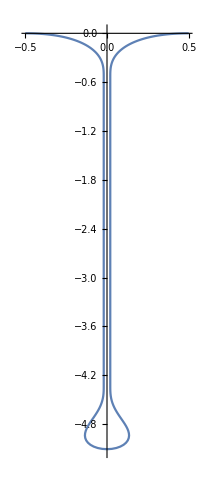

```mathematica
ParametricPlot[{{-x[S],-y[S]},{x[S],-y[S]}}/.grs[[Length[grs],6]],{S, 0, 1/2},PlotRange-> Full]
```

```mathematica
Log[grs[[10, 1]][0]]
```

0.243951

```mathematica
II={1,5,10,12,14,18, 20,21,22,23,24,26,27,32,36,37,156,224,336,759,1436,2256};
Length[II]
```

22

```mathematica
GRS=Table[grs[[II[[i]]]],{i, 1, Length[II]}];
```

```mathematica
Get["~/Documents/MorphoCrypt/Mathematica/Solutions/fullmorphology_nu_10_kf_0p01_L_1_sigma_current_2w_Q_10_N_2_w0_0p02", GRS];
```

Get::notencode: Warning: the file "~/Documents/MorphoCrypt/Mathematica/Solutions/fullmorphology_nu_10_kf_0p01_L_1_sigma_current_2w_Q_10_N_2_w0_0p02" is not encoded.

```mathematica
0.5*(Log[GRS[[22,1]][0]] + Log[GRS[[22,1]][0]])
```

5.25002

```mathematica
S0Mesh = Range[0, 0.5, 0.0001];
```

```mathematica
0.05*ConstantArray[1, Length[S0Mesh]];
```

```mathematica
data=Table[0.5*(({x[S0Mesh[[i]]], y[S0Mesh[[i]]], W[s[S0Mesh[[i]]]]}/.GRS[[20, 6]]) + ({x[S0Mesh[[i]]], y[S0Mesh[[i]]], W[s[S0Mesh[[i]]]]}/.GRS[[20,6]])),{i, 1, Length[S0Mesh]}];
Export["~/Documents/MorphoCrypt/Mathematica/Solutions/sols_fullmorphology_nu_10_k_50_1_L_1_sigma_current_2w_Q_10_N_2_w0_0p02_T_4p75.csv",data, "CSV"];
```

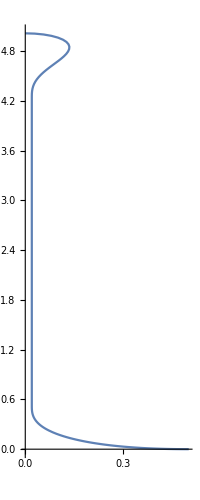

```mathematica
ParametricPlot[{x[S],y[S]}/.GRS[[22,6]],{S, 0, 0.5},PlotRange-> All]
```